```mathematica
funcZ10[k1_,k2_,k12_,e1_,e2_]=(2 e2 k12+e1 (k1-k2+√(k1^2+4 k12^2-2 k1 k2+k2^2)))/((k1-k2+√(k1^2+4 k12^2-2 k1 k2+k2^2)) √(1+(4 k12^2)/((k1-k2+√(k1^2+4 k12^2-2 k1 k2+k2^2))^2)))
```

(2 e2 k12+e1 (k1-k2+√(k1^2+4 k12^2-2 k1 k2+k2^2)))/((k1-k2+√(k1^2+4 k12^2-2 k1 k2+k2^2)) √(1+(4 k12^2)/((k1-k2+√(k1^2+4 k12^2-2 k1 k2+k2^2))^2)))

```mathematica
funcZ20[k1_,k2_,k12_,e1_,e2_]=(-2 e1 k12+e2 (k1-k2+√(k1^2+4 k12^2-2 k1 k2+k2^2)))/((k1-k2+√(k1^2+4 k12^2-2 k1 k2+k2^2)) √(1+(4 k12^2)/((k1-k2+√(k1^2+4 k12^2-2 k1 k2+k2^2))^2)))
```

(-2 e1 k12+e2 (k1-k2+√(k1^2+4 k12^2-2 k1 k2+k2^2)))/((k1-k2+√(k1^2+4 k12^2-2 k1 k2+k2^2)) √(1+(4 k12^2)/((k1-k2+√(k1^2+4 k12^2-2 k1 k2+k2^2))^2)))

```mathematica
funcgamma10[k1_,k2_,k12_,BGamma1_,BGamma2_]=(BGamma2 k12 (-k1+2 k12+k2-√(k1^2+4 k12^2-2 k1 k2+k2^2))+BGamma1 (k1^2+2 k12^2-k12 k2+k2^2+k12 √(k1^2+4 k12^2-2 k1 k2+k2^2)-k2 √(k1^2+4 k12^2-2 k1 k2+k2^2)+k1 (k12-2 k2+√(k1^2+4 k12^2-2 k1 k2+k2^2))))/(k1^2+4 k12^2+k2 (k2-√(k1^2+4 k12^2-2 k1 k2+k2^2))+k1 (-2 k2+√(k1^2+4 k12^2-2 k1 k2+k2^2)))
```

(BGamma2 k12 (-k1+2 k12+k2-√(k1^2+4 k12^2-2 k1 k2+k2^2))+BGamma1 (k1^2+2 k12^2-k12 k2+k2^2+k12 √(k1^2+4 k12^2-2 k1 k2+k2^2)-k2 √(k1^2+4 k12^2-2 k1 k2+k2^2)+k1 (k12-2 k2+√(k1^2+4 k12^2-2 k1 k2+k2^2))))/(k1^2+4 k12^2+k2 (k2-√(k1^2+4 k12^2-2 k1 k2+k2^2))+k1 (-2 k2+√(k1^2+4 k12^2-2 k1 k2+k2^2)))

```mathematica
funcgamma20[k1_,k2_,k12_,BGamma1_,BGamma2_]=(BGamma1 k12 (k1+2 k12-k2+√(k1^2+4 k12^2-2 k1 k2+k2^2))+BGamma2 (k1^2+2 k12^2+k12 k2+k2^2-k12 √(k1^2+4 k12^2-2 k1 k2+k2^2)-k2 √(k1^2+4 k12^2-2 k1 k2+k2^2)+k1 (-k12-2 k2+√(k1^2+4 k12^2-2 k1 k2+k2^2))))/(k1^2+4 k12^2+k2 (k2-√(k1^2+4 k12^2-2 k1 k2+k2^2))+k1 (-2 k2+√(k1^2+4 k12^2-2 k1 k2+k2^2)))
```

(BGamma1 k12 (k1+2 k12-k2+√(k1^2+4 k12^2-2 k1 k2+k2^2))+BGamma2 (k1^2+2 k12^2+k12 k2+k2^2-k12 √(k1^2+4 k12^2-2 k1 k2+k2^2)-k2 √(k1^2+4 k12^2-2 k1 k2+k2^2)+k1 (-k12-2 k2+√(k1^2+4 k12^2-2 k1 k2+k2^2))))/(k1^2+4 k12^2+k2 (k2-√(k1^2+4 k12^2-2 k1 k2+k2^2))+k1 (-2 k2+√(k1^2+4 k12^2-2 k1 k2+k2^2)))

```mathematica
funcgamma120[k1_,k2_,k12_,BGamma1_,BGamma2_]=((BGamma1-BGamma2) k12 (k1-k2+√(k1^2+4 k12^2-2 k1 k2+k2^2)))/(k1^2+4 k12^2+k2 (k2-√(k1^2+4 k12^2-2 k1 k2+k2^2))+k1 (-2 k2+√(k1^2+4 k12^2-2 k1 k2+k2^2)))
```

((BGamma1-BGamma2) k12 (k1-k2+√(k1^2+4 k12^2-2 k1 k2+k2^2)))/(k1^2+4 k12^2+k2 (k2-√(k1^2+4 k12^2-2 k1 k2+k2^2))+k1 (-2 k2+√(k1^2+4 k12^2-2 k1 k2+k2^2)))

```mathematica
FunctE[omega_,omega1_,omega2_,gamma1_,gamma2_,gamma12_,z1_,z2_]=-Im[(z1^2+(ⅈ gamma12 omega z1 z2)/(ⅈ (gamma12+gamma2) omega-omega^2+omega2^2))/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2+(gamma12^2 omega^2)/(ⅈ (gamma12+gamma2) omega-omega^2+omega2^2))+((ⅈ gamma12 omega z1 z2)/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2)+z2^2)/(ⅈ (gamma12+gamma2) omega-omega^2+(gamma12^2 omega^2)/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2)+omega2^2)]
```

-Im[(z1^2+(ⅈ gamma12 omega z1 z2)/(ⅈ (gamma12+gamma2) omega-omega^2+omega2^2))/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2+(gamma12^2 omega^2)/(ⅈ (gamma12+gamma2) omega-omega^2+omega2^2))+((ⅈ gamma12 omega z1 z2)/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2)+z2^2)/(ⅈ (gamma12+gamma2) omega-omega^2+(gamma12^2 omega^2)/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2)+omega2^2)]

```mathematica
FunctESLO[omega_,omega2_,gamma2_,gamma12_,z2_]=-Im[((ⅈ gamma12 omega z1 z2)/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2)+z2^2)/(ⅈ (gamma12+gamma2) omega-omega^2+(gamma12^2 omega^2)/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2)+omega2^2)]
```

-Im[((ⅈ gamma12 omega z1 z2)/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2)+z2^2)/(ⅈ (gamma12+gamma2) omega-omega^2+(gamma12^2 omega^2)/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2)+omega2^2)]

```mathematica
GammaOmega[omega_, gammar_,energyr_]=gammar*omega/energyr
```

(gammar omega)/energyr

```mathematica
FunctESMLO[omega_,omega2_,gamma2_,gamma12_,z2_]=FunctESLO[omega,omega2,GammaOmega[omega, gamma2, omega2],gamma12,z2]
```

-Im[((ⅈ gamma12 omega z1 z2)/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2)+z2^2)/(-omega^2+(gamma12^2 omega^2)/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2)+ⅈ omega (gamma12+(gamma2 omega)/omega2)+omega2^2)]

```mathematica
FunctETSE[omega_,omega1_,omega2_,gamma1_,gamma2_,gamma12_,z1_,z2_]=FunctE[omega, omega1,omega2,GammaOmega[omega, gamma1, omega1],GammaOmega[omega, gamma2, omega2],gamma12,z1,z2]
```

-Im[(z1^2+(ⅈ gamma12 omega z1 z2)/(-omega^2+ⅈ omega (gamma12+(gamma2 omega)/omega2)+omega2^2))/(-omega^2+ⅈ omega (gamma12+(gamma1 omega)/omega1)+omega1^2+(gamma12^2 omega^2)/(-omega^2+ⅈ omega (gamma12+(gamma2 omega)/omega2)+omega2^2))+((ⅈ gamma12 omega z1 z2)/(-omega^2+ⅈ omega (gamma12+(gamma1 omega)/omega1)+omega1^2)+z2^2)/(-omega^2+(gamma12^2 omega^2)/(-omega^2+ⅈ omega (gamma12+(gamma1 omega)/omega1)+omega1^2)+ⅈ omega (gamma12+(gamma2 omega)/omega2)+omega2^2)]

```mathematica
FunctETSEGDR[omega_,omega1_,omega2_,gamma1_,gamma2_,gamma12_,z1_,z2_]=FunctE[omega, omega1,omega2,GammaOmega[omega, gamma1, omega1],gamma2,gamma12,z1,z2]
```

-Im[(z1^2+(ⅈ gamma12 omega z1 z2)/(ⅈ (gamma12+gamma2) omega-omega^2+omega2^2))/(-omega^2+ⅈ omega (gamma12+(gamma1 omega)/omega1)+omega1^2+(gamma12^2 omega^2)/(ⅈ (gamma12+gamma2) omega-omega^2+omega2^2))+((ⅈ gamma12 omega z1 z2)/(-omega^2+ⅈ omega (gamma12+(gamma1 omega)/omega1)+omega1^2)+z2^2)/(ⅈ (gamma12+gamma2) omega-omega^2+(gamma12^2 omega^2)/(-omega^2+ⅈ omega (gamma12+(gamma1 omega)/omega1)+omega1^2)+omega2^2)]

```mathematica
FunctE1[omega_,omega1_,omega2_,gamma1_,gamma2_,gamma12_,z1_,z2_]=-Im[(z1^2+(ⅈ gamma12 omega z1 z2)/(ⅈ (gamma12+gamma2) omega-omega^2+omega2^2))/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2+(gamma12^2 omega^2)/(ⅈ (gamma12+gamma2) omega-omega^2+omega2^2))]
```

-Im[(z1^2+(ⅈ gamma12 omega z1 z2)/(ⅈ (gamma12+gamma2) omega-omega^2+omega2^2))/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2+(gamma12^2 omega^2)/(ⅈ (gamma12+gamma2) omega-omega^2+omega2^2))]

```mathematica
FunctE2[omega_,omega1_,omega2_,gamma1_,gamma2_,gamma12_,z1_,z2_]=-Im[((ⅈ gamma12 omega z1 z2)/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2)+z2^2)/(ⅈ (gamma12+gamma2) omega-omega^2+(gamma12^2 omega^2)/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2)+omega2^2)]
```

-Im[((ⅈ gamma12 omega z1 z2)/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2)+z2^2)/(ⅈ (gamma12+gamma2) omega-omega^2+(gamma12^2 omega^2)/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2)+omega2^2)]

```mathematica
FunctEOriginalUnnorm[omega_,k1_,k2_,k12_,BGamma1_,BGamma2_,e1_,e2_]=FunctE[omega,funcomega10[k1,k2,k12],funcomega20[k1,k2,k12],funcgamma10[k1,k2,k12,BGamma1,BGamma2],funcgamma20[k1,k2,k12,BGamma1,BGamma2],funcgamma120[k1,k2,k12,BGamma1,BGamma2],funcZ10[k1,k2,k12,e1,e2],funcZ20[k1,k2,k12,e1,e2]];
```

```mathematica
A=208;(*Pb 208*)
apar=A/10;
R0=1.2*A^(1/3);
omegar=2;     (* energy of the low energy *)
Eshell=-12.840;(*Pb 208*)
E2low=4.0854(* GQR energy PB208 exp*)
E2low=65.*A^(-5/6)/(1+0.05*Eshell) (* E2 low state energy*)
omegaf=E2low
Er=1*64.7/A^(1./3)(* GQR energy*)
omegar=Er
Gammar=17.5/A^(1./3)(* GQR energy*)
Energyr=Er;
```

4.0854

2.12476

2.12476

10.9198

10.9198

2.95359

```mathematica
Er1=15.;
Er2=1.;
Gr1=2.;
Gr2=1.;
funcZ10[Sqrt[Er1],Sqrt[Er2],Sqrt[Er1-Er2],1,1]
funcZ20[Sqrt[Er1],Sqrt[Er2],Sqrt[Er1-Er2],1,1]
funcgamma10[Sqrt[Er1],Sqrt[Er2],Sqrt[Er1-Er2],Gr1,Gr2]
funcgamma20[Sqrt[Er1],Sqrt[Er2],Sqrt[Er1-Er2],Gr1,Gr2]
funcgamma120[Sqrt[Er1],Sqrt[Er2],Sqrt[Er1-Er2],Gr1,Gr2]
```

1.39053

0.257753

2.14599

1.78758

0.466782

```mathematica
MainDirecroty=NotebookDirectory[]
```

C:\Users\beeff\go\src\github.com\orsenkucher\f1\cd106\

```mathematica
Filename="group_se_34_78.dat";
DataExp=ReadList[FileNameJoin[{MainDirecroty,Filename}],Number];
Ncolumbs=3;
Nmaxpoints1=Length[DataExp]/Ncolumbs-1;
X1aver=Table[DataExp[[Ncolumbs*i+1]],{i,0,Nmaxpoints1}];
Y1aver=Table[DataExp[[Ncolumbs*i+2]],{i,0,Nmaxpoints1}];
dY1aver=Table[DataExp[[Ncolumbs*i+3]],{i,0,Nmaxpoints1}];
Clear[DataExp]
Filename="dat2.txt";
DataExp=ReadList[FileNameJoin[{MainDirecroty,Filename}],Number];
Ncolumbs=3;
Nmaxpoints2=Length[DataExp]/Ncolumbs-1;
X2aver=Table[DataExp[[Ncolumbs*i+1]],{i,0,Nmaxpoints2}];
Y2aver=Table[DataExp[[Ncolumbs*i+2]],{i,0,Nmaxpoints2}];
dY2aver=Table[DataExp[[Ncolumbs*i+3]],{i,0,Nmaxpoints2}];
Clear[DataExp]
```

```mathematica
Needs["ErrorBarPlots`"]
```

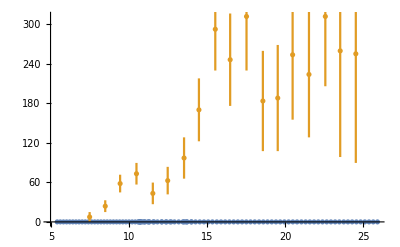

```mathematica
ErrorListPlot[{Transpose[{X1aver,Y1aver,dY1aver}],Transpose[{X2aver,Y2aver,dY2aver}]},PlotRange->All]
```

```mathematica
Data1
```

{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7}}

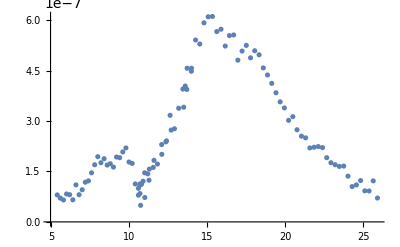

```mathematica
ListPlot[Data1]
```

```mathematica
FordY1aver
```

{5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}

94

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

{5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}

NonlinearModelFit::precw: The precision of the data and model function (MachinePrecision) is less than the specified WorkingPrecision (32).

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

FittedModel[-omega Im[(1+((«1») omega)/(«78»+«57» ⅈ omega-omega^2))/(256.+«57» ⅈ omega-omega^2+(«78» omega^2)/(«78»+«1»-omega^2))+(«21»+(«1»)/(«1»))/(«78»+«1»-«1»+(«78»«1»«1»)/(«1»))]]

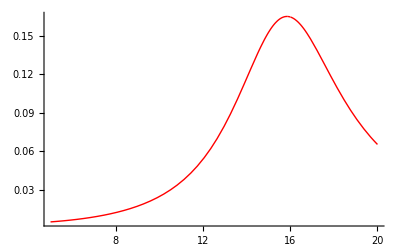

FittedModel::precw: The precision of the argument function (MachinePrecision) is less than WorkingPrecision (32).

16.

FittedModel::precw: The precision of the argument function (MachinePrecision) is less than WorkingPrecision (32).

2.271416340334173611381629598327

FittedModel::precw: The precision of the argument function (MachinePrecision) is less than WorkingPrecision (32).

4.256487043232616507282273232704

FittedModel::precw: The precision of the argument function (MachinePrecision) is less than WorkingPrecision (32).

2.

FittedModel::precw: The precision of the argument function (MachinePrecision) is less than WorkingPrecision (32).

1.893549526640985636305458683637

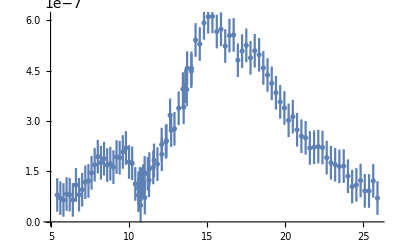

FittedModel::precw: The precision of the argument function (MachinePrecision) is less than WorkingPrecision (32).

| Estimate | Standard Error | t-Statistic | P-Value
omega1p | 16. | 0.453011 | 35.3192 | 1.57356×10^-54
omega2p | 2.271416340334173611381629598327 | 1.28935 | 1.76168 | 0.08152
Gamma1p | 4.256487043232616507282273232704 | 0.489863 | 8.68914 | 1.52562×10^-13
Gamma2p | 2. | 3.24948 | 0.615483 | 0.539789
Gamma12p | 1.893549526640985636305458683637 | 0.426704 | 4.43762 | 0.0000257084

FittedModel::precw: The precision of the argument function (MachinePrecision) is less than WorkingPrecision (32).

{{16.,0.453011,35.3192,1.57356×10^-54},{2.271416340334173611381629598327,1.28935,1.76168,0.08152},{4.256487043232616507282273232704,0.489863,8.68914,1.52562×10^-13},{2.,3.24948,0.615483,0.539789},{1.893549526640985636305458683637,0.426704,4.43762,0.0000257084}}

```mathematica
Nmaxpointstemp=Length[Y1aver]-7
FordY1aver=Table[1,{i,1,Nmaxpointstemp+1}]
FordY1aver=Table[dY1aver[[i]],{i,1,Nmaxpointstemp+1}]
Data1=Table[{X1aver[[i]],Y1aver[[i]]},{i,1,Nmaxpointstemp+1}];
model=omega*FunctE[omega,omega1p,omega2p,Gamma1p,Gamma2p,Gamma12p,1,0.1];
FITtemp=NonlinearModelFit[Data1,model,{{omega1p,16},{omega2p,10},{Gamma1p,3},{Gamma2p,2},{Gamma12p,0.001}}, omega,Weights->1/FordY1aver^2,WorkingPrecision->32]
Plot[FITtemp[x],{x,5,20},Epilog:>Point[Data1],PlotStyle->{Red,Thick},PlotRange->All]
Par1=omega1p/.FITtemp["BestFitParameters"]
Par2=omega2p/.FITtemp["BestFitParameters"]
Par3=Gamma1p/.FITtemp["BestFitParameters"]
Par4=Gamma2p/.FITtemp["BestFitParameters"]
Par5=Gamma12p/.FITtemp["BestFitParameters"]
ResponseFunc[omega_]=model/.{omega1p-> Par1 ,omega2p-> Par2,Gamma1p-> Par3,Gamma2p-> Par4,Gamma12p-> Par5};
Show[ErrorListPlot[Transpose[{X1aver,Y1aver,dY1aver}],PlotRange->All],ListPlot[{Transpose[{X1aver,ResponseFunc[X1aver]}],Transpose[{X1aver,ResponseFunc[X1aver]}]},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
FITtemp["ParameterTable"]
vals=FITtemp["ParameterTableEntries"]
```

-Graphics-

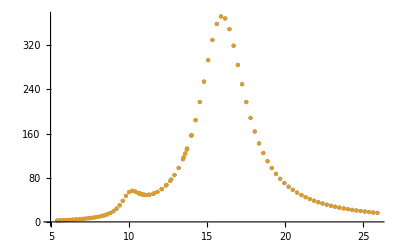

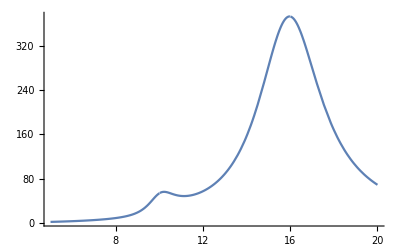

```mathematica
Er1=16.;
Er2=10.;
Gr1=3.;
Gr2=1.;
Gr12=0.5;
zconst=36;
Z1t=zconst;
Z2t=zconst*0.2;
TESTSigma[omega_]=omega*FunctE[omega,Er1,Er2,Gr1,Gr2,Gr12,Z1t,Z2t];
Show[ErrorListPlot[Transpose[{X1aver,Y1aver,dY1aver}],PlotRange->All],ListPlot[{Transpose[{X1aver,TESTSigma[X1aver]}],Transpose[{X1aver,TESTSigma[X1aver]}]},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
ListPlot[{Transpose[{X1aver,TESTSigma[X1aver]}],Transpose[{X1aver,TESTSigma[X1aver]}]},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]
Plot[TESTSigma[x],{x,5,20},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]
```

```mathematica
(* Fit  the cross section in the region [Ulow,Uupper] *)
```

```mathematica
Ulow=5.0;
Uupper=25.0;
Nlow=1;
Nupper=Length[Y1aver]
Do[If[X1aver[[i]]<Ulow,Nlow=i,Nlow=Nlow],{i,1,Length[Y1aver]}];
Do[If[X1aver[[i]]<Uupper,Nupper=i,Nupper=Nupper],{i,1,Length[Y1aver]}];
Nlow
Nupper
```

101

1

101

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

Part::partw: Part 102 of {5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,«51»} does not exist.

{5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,{5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧}

Part::partw: Part 102 of {5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,«51»} does not exist.

Part::partw: Part 102 of {8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,«7»,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,«51»} does not exist.

Part::partw: Part 102 of {5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,«51»} does not exist.

Part::partw: Part 102 of {8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,«7»,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,«51»} does not exist.

Part::partw: Part 102 of {5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,«51»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

NonlinearModelFit::wts: The value of option Weights -> {4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,«33»,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,«52»} should be a list of real numbers or a pure function.

NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2)+Z20^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2)+omega2p^2)],Gamma2p>0,Gamma12p>0},{{omega1p,17.},{omega2p,8.},{Gamma1p,7.},{Gamma2p,1.},{Gamma12p,0.0001},{Z10,0.1},{Z20,0.1}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2},MaxIterations→∞]

NonlinearModelFit::wts: The value of option Weights -> {4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,«33»,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,«52»} should be a list of real numbers or a pure function.

General::stop: Further output of NonlinearModelFit::wts will be suppressed during this calculation.

-Graphics-

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

omega1p/.NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2)+Z20^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2)+omega2p^2)],Gamma2p>0,Gamma12p>0},{{omega1p,17.},{omega2p,8.},{Gamma1p,7.},{Gamma2p,1.},{Gamma12p,0.0001},{Z10,0.1},{Z20,0.1}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2},MaxIterations→∞][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

omega2p/.NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2)+Z20^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2)+omega2p^2)],Gamma2p>0,Gamma12p>0},{{omega1p,17.},{omega2p,8.},{Gamma1p,7.},{Gamma2p,1.},{Gamma12p,0.0001},{Z10,0.1},{Z20,0.1}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2},MaxIterations→∞][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Gamma1p/.NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2)+Z20^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2)+omega2p^2)],Gamma2p>0,Gamma12p>0},{{omega1p,17.},{omega2p,8.},{Gamma1p,7.},{Gamma2p,1.},{Gamma12p,0.0001},{Z10,0.1},{Z20,0.1}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2},MaxIterations→∞][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Gamma2p/.NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2)+Z20^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2)+omega2p^2)],Gamma2p>0,Gamma12p>0},{{omega1p,17.},{omega2p,8.},{Gamma1p,7.},{Gamma2p,1.},{Gamma12p,0.0001},{Z10,0.1},{Z20,0.1}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2},MaxIterations→∞][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Gamma12p/.NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2)+Z20^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2)+omega2p^2)],Gamma2p>0,Gamma12p>0},{{omega1p,17.},{omega2p,8.},{Gamma1p,7.},{Gamma2p,1.},{Gamma12p,0.0001},{Z10,0.1},{Z20,0.1}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2},MaxIterations→∞][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Z10/.NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2)+Z20^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2)+omega2p^2)],Gamma2p>0,Gamma12p>0},{{omega1p,17.},{omega2p,8.},{Gamma1p,7.},{Gamma2p,1.},{Gamma12p,0.0001},{Z10,0.1},{Z20,0.1}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2},MaxIterations→∞][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Z20/.NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2)+Z20^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2)+omega2p^2)],Gamma2p>0,Gamma12p>0},{{omega1p,17.},{omega2p,8.},{Gamma1p,7.},{Gamma2p,1.},{Gamma12p,0.0001},{Z10,0.1},{Z20,0.1}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2},MaxIterations→∞][BestFitParameters]

NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2)+Z20^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2)+omega2p^2)],Gamma2p>0,Gamma12p>0},{{omega1p,17.},{omega2p,8.},{Gamma1p,7.},{Gamma2p,1.},{Gamma12p,0.0001},{Z10,0.1},{Z20,0.1}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2},MaxIterations→∞][x]

Part::partw: Part 102 of {{1,5.4},{2,5.6},{3,5.8},{4,6.},{5,6.2},{6,6.4},{7,6.6},{8,6.8},{9,7.},{10,7.2},{11,7.4},{12,7.6},{13,7.8},{14,8.},{15,8.2},{16,8.4},{17,8.6},{18,8.8},{19,9.},{20,9.2},{21,9.4},«10»,{32,12.09},{33,12.36},{34,12.63},{35,12.91},{36,13.18},{37,13.45},{38,13.72},{39,13.99},{40,14.26},{41,14.53},{42,14.8},{43,15.07},{44,15.34},{45,15.62},{46,15.89},{47,16.16},{48,16.43},{49,16.7},{50,16.97},«51»} does not exist.

Part::partw: Part 102 of {{1,8.02×10^-8},{2,7.06×10^-8},{3,6.52×10^-8},{4,8.3×10^-8},{5,8.09×10^-8},{6,6.56×10^-8},{7,1.1×10^-7},{8,8.08×10^-8},{9,9.56×10^-8},{10,1.18×10^-7},{11,1.22×10^-7},{12,1.46×10^-7},{13,1.7×10^-7},{14,1.94×10^-7},{15,1.76×10^-7},«21»,{37,3.95×10^-7},{38,4.57×10^-7},{39,4.48×10^-7},{40,5.41×10^-7},{41,5.29×10^-7},{42,5.92×10^-7},{43,6.1×10^-7},{44,6.11×10^-7},{45,5.66×10^-7},{46,5.73×10^-7},{47,5.23×10^-7},{48,5.54×10^-7},{49,5.56×10^-7},{50,4.81×10^-7},«51»} does not exist.

Part::partw: Part 102 of {{1,5.×10^-8},{2,5.×10^-8},{3,5.×10^-8},{4,5.×10^-8},{5,5.×10^-8},{6,5.×10^-8},{7,5.×10^-8},{8,5.×10^-8},{9,5.×10^-8},{10,5.×10^-8},{11,5.×10^-8},{12,5.×10^-8},{13,5.×10^-8},{14,5.×10^-8},{15,5.×10^-8},{16,5.×10^-8},{17,5.×10^-8},«17»,{35,5.×10^-8},{36,5.×10^-8},{37,5.×10^-8},{38,5.×10^-8},{39,5.×10^-8},{40,5.×10^-8},{41,5.×10^-8},{42,5.×10^-8},{43,5.×10^-8},{44,5.×10^-8},{45,5.×10^-8},{46,5.×10^-8},{47,5.×10^-8},{48,5.×10^-8},{49,5.×10^-8},{50,5.×10^-8},«51»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

NonlinearModelFit::wts: The value of option Weights -> {4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,«33»,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,«52»} should be a list of real numbers or a pure function.

General::stop: Further output of NonlinearModelFit::wts will be suppressed during this calculation.

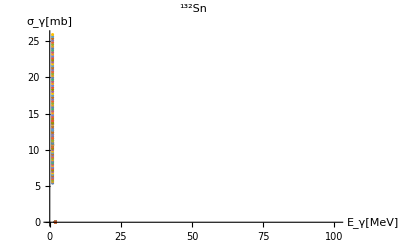

C:\Users\beeff\go\src\github.com\orsenkucher\f1\cd106\FigSigmaFit132Sn.eps

NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2)+Z20^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2)+omega2p^2)],Gamma2p>0,Gamma12p>0},{{omega1p,17.},{omega2p,8.},{Gamma1p,7.},{Gamma2p,1.},{Gamma12p,0.0001},{Z10,0.1},{Z20,0.1}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2},MaxIterations→∞][ParameterTable]

NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2)+Z20^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma1p) omega-omega^2+omega1p^2)+omega2p^2)],Gamma2p>0,Gamma12p>0},{{omega1p,17.},{omega2p,8.},{Gamma1p,7.},{Gamma2p,1.},{Gamma12p,0.0001},{Z10,0.1},{Z20,0.1}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2},MaxIterations→∞][ParameterTableEntries]

4.21053×10^12 FitResiduals^2

1/95 (4.×10^14 (8.02×10^-8-NonlinearModelFit[1][5.4])^2+4.×10^14 (7.06×10^-8-NonlinearModelFit[{1},4,1][5.6])^2+4.×10^14 (6.52×10^-8-1)^2+4.×10^14 1^2+94+1+4.×10^14 (1)^2+4.×10^14 (7.1×10^-8-1[25.91])^2+(({8.02×10^-8,7.06×10^-8,97,3.94×10^-7,4.57×10^-7}⟦102⟧-1)^2)/(({5.×10^-8,5.×10^-8,5.×10^-8,95,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2))
 |  |  |  |

```mathematica
(* Со связью TSE *)
Nmaxpointstemp=Nupper;
FordY1aver=Table[1,{i,1,Nmaxpointstemp+1}]
FordY1aver=Table[dY1aver[[i]],{i,1,Nmaxpointstemp+1}]
Data1=Table[{X1aver[[i]],Y1aver[[i]]},{i,1,Nmaxpointstemp+1}];
Data2plotSn132=Table[{X1aver[[i]],Y1aver[[i]],dY1aver[[i]]},{i,1,Nmaxpointstemp+1}];
model=omega*FunctE[omega,omega1p,omega2p,Gamma1p,Gamma2p,Gamma12p,Z10,Z20];
FITtemp=NonlinearModelFit[Data1,{model,Gamma2p>0,Gamma12p>0},{{omega1p,17.},{omega2p,8.},{Gamma1p,7.},{Gamma2p,1.},{Gamma12p,.0001},{Z10,.1},{Z20,.1}}, omega,Weights->1/FordY1aver^2,MaxIterations->∞]
Plot[FITtemp[x],{x,5,20},Epilog:>Point[Data1],PlotStyle->{Red,Thick}]
Par1=omega1p/.FITtemp["BestFitParameters"]
Par2=omega2p/.FITtemp["BestFitParameters"]
Par3=Gamma1p/.FITtemp["BestFitParameters"]
Par4=Gamma2p/.FITtemp["BestFitParameters"]
Par5=Gamma12p/.FITtemp["BestFitParameters"]
Par6=Z10/.FITtemp["BestFitParameters"]
Par7=Z20/.FITtemp["BestFitParameters"]
Filename="FigSigmaFit132Sn.eps";
ResponseFunc[omega_]=model/.{omega1p-> Par1 ,omega2p-> Par2,Gamma1p-> Par3,Gamma2p-> Par4,Gamma12p-> Par5,Z10-> Par6,Z20-> Par7};
plot8Data=FITtemp[x]
Show[ErrorListPlot[Data2plotSn132,PlotRange->All,PlotLabel->Style[Row[{Superscript["","132"],"Sn"}],FontFamily->"Times",18,Bold],AxesLabel->{Style[Row[{Subscript["E","γ"],"[MeV]"}],FontFamily->"Times",12,Italic],Style[Row[{Subscript["σ","γ"],"[mb]",""}],FontFamily->"Times",12,Italic]}],Plot[FITtemp[x],{x,7,25},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
Export[FileNameJoin[{MainDirecroty,Filename}],%]
FITtemp["ParameterTable"]
vals=FITtemp["ParameterTableEntries"]
Chi2=Sum[(FITtemp["FitResiduals"][[i]]/FordY1aver[[i]])^2,{i,1,Length[FITtemp["FitResiduals"]]}]/(Nmaxpointstemp+1-7)
Sum[((Data1[[i,2]]-FITtemp[Data1[[i,1]]])/FordY1aver[[i]])^2,{i,1,Length[FordY1aver]}]/(Nmaxpointstemp+1-7)
FITtemp1[x_]=FITtemp[x];
```

```mathematica
(* Без связи TSE *)
Nmaxpointstemp=Nupper;
FordY1aver=Table[1,{i,1,Nmaxpointstemp+1}]
FordY1aver=Table[dY1aver[[i]],{i,1,Nmaxpointstemp+1}]
Data1=Table[{X1aver[[i]],Y1aver[[i]]},{i,1,Nmaxpointstemp+1}];
Data2plotSn132=Table[{X1aver[[i]],Y1aver[[i]],dY1aver[[i]]},{i,1,Nmaxpointstemp+1}];
model=omega*FunctE[omega,omega1p,omega2p,Gamma1p,Gamma2p,0,Z10,Z20];
FITtemp=NonlinearModelFit[Data1,{model,Gamma2p>0},{{omega1p,16},{omega2p,10},{Gamma1p,3},{Gamma2p,2},{Z10,36},{Z20,0.1*36}}, omega,Weights->1/FordY1aver^2,MaxIterations->∞]
Plot[FITtemp[x],{x,5,20},Epilog:>Point[Data1],PlotStyle->{Red,Thick}]
Par1=omega1p/.FITtemp["BestFitParameters"]
Par2=omega2p/.FITtemp["BestFitParameters"]
Par3=Gamma1p/.FITtemp["BestFitParameters"]
Par4=Gamma2p/.FITtemp["BestFitParameters"]
Par5=Z10/.FITtemp["BestFitParameters"]
Par6=Z20/.FITtemp["BestFitParameters"]
Filename="FigSigmaFit132Sn.eps";
ResponseFunc[omega_]=model/.{omega1p-> Par1 ,omega2p-> Par2,Gamma1p-> Par3,Gamma2p-> Par4,Z10-> Par5,Z20-> Par6};
plot7Data=FITtemp[x]
Show[ErrorListPlot[Data2plotSn132,PlotRange->All,PlotLabel->Style[Row[{Superscript["","132"],"Sn"}],FontFamily->"Times",18,Bold],AxesLabel->{Style[Row[{Subscript["E","γ"],"[MeV]"}],FontFamily->"Times",12,Italic],Style[Row[{Subscript["σ","γ"],"[mb]",""}],FontFamily->"Times",12,Italic]}],Plot[FITtemp[x],{x,7,25},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
Export[FileNameJoin[{MainDirecroty,Filename}],%]
FITtemp["ParameterTable"]
vals=FITtemp["ParameterTableEntries"]
Chi2=Sum[(FITtemp["FitResiduals"][[i]]/FordY1aver[[i]])^2,{i,1,Length[FITtemp["FitResiduals"]]}]/(Nmaxpointstemp+1-6)
Sum[((Data1[[i,2]]-FITtemp[Data1[[i,1]]])/FordY1aver[[i]])^2,{i,1,Length[FordY1aver]}]/(Nmaxpointstemp+1-6)
FITtemp1[x_]=FITtemp[x];
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

Part::partw: Part 102 of {5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,«51»} does not exist.

{5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,{5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧}

Part::partw: Part 102 of {5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,«51»} does not exist.

Part::partw: Part 102 of {8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,«7»,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,«51»} does not exist.

Part::partw: Part 102 of {5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,«51»} does not exist.

Part::partw: Part 102 of {8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,«7»,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,«51»} does not exist.

Part::partw: Part 102 of {5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,«51»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

NonlinearModelFit::wts: The value of option Weights -> {4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,«33»,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,«52»} should be a list of real numbers or a pure function.

NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[Z10^2/(ⅈ Gamma1p omega-omega^2+omega1p^2)+Z20^2/(ⅈ Gamma2p omega-omega^2+omega2p^2)],Gamma2p>0},{{omega1p,16},{omega2p,10},{Gamma1p,3},{Gamma2p,2},{Z10,36},{Z20,3.6}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2},MaxIterations→∞]

NonlinearModelFit::wts: The value of option Weights -> {4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,«33»,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,«52»} should be a list of real numbers or a pure function.

General::stop: Further output of NonlinearModelFit::wts will be suppressed during this calculation.

-Graphics-

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

omega1p/.NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[Z10^2/(ⅈ Gamma1p omega-omega^2+omega1p^2)+Z20^2/(ⅈ Gamma2p omega-omega^2+omega2p^2)],Gamma2p>0},{{omega1p,16},{omega2p,10},{Gamma1p,3},{Gamma2p,2},{Z10,36},{Z20,3.6}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2},MaxIterations→∞][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

omega2p/.NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[Z10^2/(ⅈ Gamma1p omega-omega^2+omega1p^2)+Z20^2/(ⅈ Gamma2p omega-omega^2+omega2p^2)],Gamma2p>0},{{omega1p,16},{omega2p,10},{Gamma1p,3},{Gamma2p,2},{Z10,36},{Z20,3.6}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2},MaxIterations→∞][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Gamma1p/.NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[Z10^2/(ⅈ Gamma1p omega-omega^2+omega1p^2)+Z20^2/(ⅈ Gamma2p omega-omega^2+omega2p^2)],Gamma2p>0},{{omega1p,16},{omega2p,10},{Gamma1p,3},{Gamma2p,2},{Z10,36},{Z20,3.6}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2},MaxIterations→∞][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Gamma2p/.NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[Z10^2/(ⅈ Gamma1p omega-omega^2+omega1p^2)+Z20^2/(ⅈ Gamma2p omega-omega^2+omega2p^2)],Gamma2p>0},{{omega1p,16},{omega2p,10},{Gamma1p,3},{Gamma2p,2},{Z10,36},{Z20,3.6}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2},MaxIterations→∞][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Z10/.NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[Z10^2/(ⅈ Gamma1p omega-omega^2+omega1p^2)+Z20^2/(ⅈ Gamma2p omega-omega^2+omega2p^2)],Gamma2p>0},{{omega1p,16},{omega2p,10},{Gamma1p,3},{Gamma2p,2},{Z10,36},{Z20,3.6}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2},MaxIterations→∞][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Z20/.NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[Z10^2/(ⅈ Gamma1p omega-omega^2+omega1p^2)+Z20^2/(ⅈ Gamma2p omega-omega^2+omega2p^2)],Gamma2p>0},{{omega1p,16},{omega2p,10},{Gamma1p,3},{Gamma2p,2},{Z10,36},{Z20,3.6}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2},MaxIterations→∞][BestFitParameters]

NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[Z10^2/(ⅈ Gamma1p omega-omega^2+omega1p^2)+Z20^2/(ⅈ Gamma2p omega-omega^2+omega2p^2)],Gamma2p>0},{{omega1p,16},{omega2p,10},{Gamma1p,3},{Gamma2p,2},{Z10,36},{Z20,3.6}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2},MaxIterations→∞][x]

Part::partw: Part 102 of {{1,5.4},{2,5.6},{3,5.8},{4,6.},{5,6.2},{6,6.4},{7,6.6},{8,6.8},{9,7.},{10,7.2},{11,7.4},{12,7.6},{13,7.8},{14,8.},{15,8.2},{16,8.4},{17,8.6},{18,8.8},{19,9.},{20,9.2},{21,9.4},«10»,{32,12.09},{33,12.36},{34,12.63},{35,12.91},{36,13.18},{37,13.45},{38,13.72},{39,13.99},{40,14.26},{41,14.53},{42,14.8},{43,15.07},{44,15.34},{45,15.62},{46,15.89},{47,16.16},{48,16.43},{49,16.7},{50,16.97},«51»} does not exist.

Part::partw: Part 102 of {{1,8.02×10^-8},{2,7.06×10^-8},{3,6.52×10^-8},{4,8.3×10^-8},{5,8.09×10^-8},{6,6.56×10^-8},{7,1.1×10^-7},{8,8.08×10^-8},{9,9.56×10^-8},{10,1.18×10^-7},{11,1.22×10^-7},{12,1.46×10^-7},{13,1.7×10^-7},{14,1.94×10^-7},{15,1.76×10^-7},«21»,{37,3.95×10^-7},{38,4.57×10^-7},{39,4.48×10^-7},{40,5.41×10^-7},{41,5.29×10^-7},{42,5.92×10^-7},{43,6.1×10^-7},{44,6.11×10^-7},{45,5.66×10^-7},{46,5.73×10^-7},{47,5.23×10^-7},{48,5.54×10^-7},{49,5.56×10^-7},{50,4.81×10^-7},«51»} does not exist.

Part::partw: Part 102 of {{1,5.×10^-8},{2,5.×10^-8},{3,5.×10^-8},{4,5.×10^-8},{5,5.×10^-8},{6,5.×10^-8},{7,5.×10^-8},{8,5.×10^-8},{9,5.×10^-8},{10,5.×10^-8},{11,5.×10^-8},{12,5.×10^-8},{13,5.×10^-8},{14,5.×10^-8},{15,5.×10^-8},{16,5.×10^-8},{17,5.×10^-8},«17»,{35,5.×10^-8},{36,5.×10^-8},{37,5.×10^-8},{38,5.×10^-8},{39,5.×10^-8},{40,5.×10^-8},{41,5.×10^-8},{42,5.×10^-8},{43,5.×10^-8},{44,5.×10^-8},{45,5.×10^-8},{46,5.×10^-8},{47,5.×10^-8},{48,5.×10^-8},{49,5.×10^-8},{50,5.×10^-8},«51»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

NonlinearModelFit::wts: The value of option Weights -> {4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,«33»,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,«52»} should be a list of real numbers or a pure function.

General::stop: Further output of NonlinearModelFit::wts will be suppressed during this calculation.

-Graphics-

C:\Users\beeff\go\src\github.com\orsenkucher\f1\cd106\FigSigmaFit132Sn.eps

NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[Z10^2/(ⅈ Gamma1p omega-omega^2+omega1p^2)+Z20^2/(ⅈ Gamma2p omega-omega^2+omega2p^2)],Gamma2p>0},{{omega1p,16},{omega2p,10},{Gamma1p,3},{Gamma2p,2},{Z10,36},{Z20,3.6}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2},MaxIterations→∞][ParameterTable]

NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[Z10^2/(ⅈ Gamma1p omega-omega^2+omega1p^2)+Z20^2/(ⅈ Gamma2p omega-omega^2+omega2p^2)],Gamma2p>0},{{omega1p,16},{omega2p,10},{Gamma1p,3},{Gamma2p,2},{Z10,36},{Z20,3.6}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2},MaxIterations→∞][ParameterTableEntries]

4.16667×10^12 FitResiduals^2

1/96 (4.×10^14 (8.02×10^-8-NonlinearModelFit[1][5.4])^2+4.×10^14 (7.06×10^-8-NonlinearModelFit[{1},4,1][5.6])^2+4.×10^14 (6.52×10^-8-1)^2+4.×10^14 1^2+94+1+4.×10^14 (1)^2+4.×10^14 (7.1×10^-8-1[25.91])^2+(({8.02×10^-8,7.06×10^-8,97,3.94×10^-7,4.57×10^-7}⟦102⟧-1)^2)/(({5.×10^-8,5.×10^-8,5.×10^-8,95,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2))
 |  |  |  |

```mathematica
(* Без связи SLO *)
Nmaxpointstemp=Nupper;
FordY1aver=Table[1,{i,1,Nmaxpointstemp+1}]
FordY1aver=Table[dY1aver[[i]],{i,1,Nmaxpointstemp+1}]
Data1=Table[{X1aver[[i]],Y1aver[[i]]},{i,1,Nmaxpointstemp+1}];
Data2plotSn132=Table[{X1aver[[i]],Y1aver[[i]],dY1aver[[i]]},{i,1,Nmaxpointstemp+1}];
model=omega*FunctESLO[omega,omega2p,Gamma2p,0,Z20];
FITtemp=NonlinearModelFit[Data1,{model,Gamma2p>0},{{omega2p,10},{Gamma2p,2},{Z20,0.1*36}}, omega,Weights->1/FordY1aver^2]
Plot[FITtemp[x],{x,5,20},Epilog:>Point[Data1],PlotStyle->{Red,Thick}]
Par1=omega2p/.FITtemp["BestFitParameters"]
Par2=Gamma2p/.FITtemp["BestFitParameters"]
Par3=Z20/.FITtemp["BestFitParameters"]
Filename="FigSigmaFit132Sn.eps";
ResponseFunc[omega_]=model/.{omega2p-> Par1,Gamma2p-> Par2,Z20-> Par3};
plot6Data=FITtemp[x]
Show[ErrorListPlot[Data2plotSn132,PlotRange->All,PlotLabel->Style[Row[{Superscript["","132"],"Sn"}],FontFamily->"Times",18,Bold],AxesLabel->{Style[Row[{Subscript["E","γ"],"[MeV]"}],FontFamily->"Times",12,Italic],Style[Row[{Subscript["σ","γ"],"[mb]",""}],FontFamily->"Times",12,Italic]}],Plot[FITtemp[x],{x,7,25},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
Export[FileNameJoin[{MainDirecroty,Filename}],%]
FITtemp["ParameterTable"]
vals=FITtemp["ParameterTableEntries"]
Chi2=Sum[(FITtemp["FitResiduals"][[i]]/FordY1aver[[i]])^2,{i,1,Length[FITtemp["FitResiduals"]]}]/(Nmaxpointstemp+1-3)
Sum[((Data1[[i,2]]-FITtemp[Data1[[i,1]]])/FordY1aver[[i]])^2,{i,1,Length[FordY1aver]}]/(Nmaxpointstemp+1-3)
FITtemp1[x_]=FITtemp[x];
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

Part::partw: Part 102 of {5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,«51»} does not exist.

{5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,{5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧}

Part::partw: Part 102 of {5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,«51»} does not exist.

Part::partw: Part 102 of {8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,«7»,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,«51»} does not exist.

Part::partw: Part 102 of {5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,«51»} does not exist.

Part::partw: Part 102 of {8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,«7»,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,«51»} does not exist.

Part::partw: Part 102 of {5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,«51»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

NonlinearModelFit::wts: The value of option Weights -> {4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,«33»,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,«52»} should be a list of real numbers or a pure function.

NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[Z20^2/(ⅈ Gamma2p omega-omega^2+omega2p^2)],Gamma2p>0},{{omega2p,10},{Gamma2p,2},{Z20,3.6}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2}]

NonlinearModelFit::wts: The value of option Weights -> {4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,«33»,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,«52»} should be a list of real numbers or a pure function.

General::stop: Further output of NonlinearModelFit::wts will be suppressed during this calculation.

-Graphics-

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

omega2p/.NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[Z20^2/(ⅈ Gamma2p omega-omega^2+omega2p^2)],Gamma2p>0},{{omega2p,10},{Gamma2p,2},{Z20,3.6}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2}][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Gamma2p/.NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[Z20^2/(ⅈ Gamma2p omega-omega^2+omega2p^2)],Gamma2p>0},{{omega2p,10},{Gamma2p,2},{Z20,3.6}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2}][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Z20/.NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[Z20^2/(ⅈ Gamma2p omega-omega^2+omega2p^2)],Gamma2p>0},{{omega2p,10},{Gamma2p,2},{Z20,3.6}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2}][BestFitParameters]

NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[Z20^2/(ⅈ Gamma2p omega-omega^2+omega2p^2)],Gamma2p>0},{{omega2p,10},{Gamma2p,2},{Z20,3.6}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2}][x]

Part::partw: Part 102 of {{1,5.4},{2,5.6},{3,5.8},{4,6.},{5,6.2},{6,6.4},{7,6.6},{8,6.8},{9,7.},{10,7.2},{11,7.4},{12,7.6},{13,7.8},{14,8.},{15,8.2},{16,8.4},{17,8.6},{18,8.8},{19,9.},{20,9.2},{21,9.4},«10»,{32,12.09},{33,12.36},{34,12.63},{35,12.91},{36,13.18},{37,13.45},{38,13.72},{39,13.99},{40,14.26},{41,14.53},{42,14.8},{43,15.07},{44,15.34},{45,15.62},{46,15.89},{47,16.16},{48,16.43},{49,16.7},{50,16.97},«51»} does not exist.

Part::partw: Part 102 of {{1,8.02×10^-8},{2,7.06×10^-8},{3,6.52×10^-8},{4,8.3×10^-8},{5,8.09×10^-8},{6,6.56×10^-8},{7,1.1×10^-7},{8,8.08×10^-8},{9,9.56×10^-8},{10,1.18×10^-7},{11,1.22×10^-7},{12,1.46×10^-7},{13,1.7×10^-7},{14,1.94×10^-7},{15,1.76×10^-7},«21»,{37,3.95×10^-7},{38,4.57×10^-7},{39,4.48×10^-7},{40,5.41×10^-7},{41,5.29×10^-7},{42,5.92×10^-7},{43,6.1×10^-7},{44,6.11×10^-7},{45,5.66×10^-7},{46,5.73×10^-7},{47,5.23×10^-7},{48,5.54×10^-7},{49,5.56×10^-7},{50,4.81×10^-7},«51»} does not exist.

Part::partw: Part 102 of {{1,5.×10^-8},{2,5.×10^-8},{3,5.×10^-8},{4,5.×10^-8},{5,5.×10^-8},{6,5.×10^-8},{7,5.×10^-8},{8,5.×10^-8},{9,5.×10^-8},{10,5.×10^-8},{11,5.×10^-8},{12,5.×10^-8},{13,5.×10^-8},{14,5.×10^-8},{15,5.×10^-8},{16,5.×10^-8},{17,5.×10^-8},«17»,{35,5.×10^-8},{36,5.×10^-8},{37,5.×10^-8},{38,5.×10^-8},{39,5.×10^-8},{40,5.×10^-8},{41,5.×10^-8},{42,5.×10^-8},{43,5.×10^-8},{44,5.×10^-8},{45,5.×10^-8},{46,5.×10^-8},{47,5.×10^-8},{48,5.×10^-8},{49,5.×10^-8},{50,5.×10^-8},«51»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

NonlinearModelFit::wts: The value of option Weights -> {4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,«33»,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,«52»} should be a list of real numbers or a pure function.

General::stop: Further output of NonlinearModelFit::wts will be suppressed during this calculation.

-Graphics-

C:\Users\beeff\go\src\github.com\orsenkucher\f1\cd106\FigSigmaFit132Sn.eps

NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[Z20^2/(ⅈ Gamma2p omega-omega^2+omega2p^2)],Gamma2p>0},{{omega2p,10},{Gamma2p,2},{Z20,3.6}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2}][ParameterTable]

NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[Z20^2/(ⅈ Gamma2p omega-omega^2+omega2p^2)],Gamma2p>0},{{omega2p,10},{Gamma2p,2},{Z20,3.6}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2}][ParameterTableEntries]

4.0404×10^12 FitResiduals^2

1/99 (4.×10^14 (8.02×10^-8-NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},96,{13.7,3.94×10^-7},{14.,4.57×10^-7},{1}},4][5.4])^2+4.×10^14 (7.06×10^-8-1[5.6])^2+4.×10^14 (1)^2+96+4.×10^14 1^2+4.×10^14 (7.1×10^-8-1)^2+(({8.02×10^-8,100}⟦102⟧-1)^2)/(({5.×10^-8,5.×10^-8,97,5.×10^-8,5.×10^-8}13⟧)^2))
 |  |  |  |

```mathematica
(* Без связи SMLO - звисимость ширины от енергии *)
Nmaxpointstemp=Nupper;
FordY1aver=Table[1,{i,1,Nmaxpointstemp+1}]
FordY1aver=Table[dY1aver[[i]],{i,1,Nmaxpointstemp+1}]
Data1=Table[{X1aver[[i]],Y1aver[[i]]},{i,1,Nmaxpointstemp+1}];
Data2plotSn132=Table[{X1aver[[i]],Y1aver[[i]],dY1aver[[i]]},{i,1,Nmaxpointstemp+1}];
model=omega*FunctESMLO[omega,omega2p,Gamma2p,0,Z20];
FITtemp=NonlinearModelFit[Data1,{model,Gamma2p>0},{{omega2p,10},{Gamma2p,2},{Z20,0.1*36}}, omega,Weights->1/FordY1aver^2]
Plot[FITtemp[x],{x,5,20},Epilog:>Point[Data1],PlotStyle->{Red,Thick}]
Par1=omega2p/.FITtemp["BestFitParameters"]
Par2=Gamma2p/.FITtemp["BestFitParameters"]
Par3=Z20/.FITtemp["BestFitParameters"]
Filename="FigSigmaFit132Sn.eps";
ResponseFunc[omega_]=model/.{omega2p-> Par1,Gamma2p-> Par2,Z20-> Par3};
plot5Data=FITtemp[x]
Show[ErrorListPlot[Data2plotSn132,PlotRange->All,PlotLabel->Style[Row[{Superscript["","132"],"Sn"}],FontFamily->"Times",18,Bold],AxesLabel->{Style[Row[{Subscript["E","γ"],"[MeV]"}],FontFamily->"Times",12,Italic],Style[Row[{Subscript["σ","γ"],"[mb]",""}],FontFamily->"Times",12,Italic]}],Plot[FITtemp[x],{x,7,25},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
Export[FileNameJoin[{MainDirecroty,Filename}],%]
FITtemp["ParameterTable"]
vals=FITtemp["ParameterTableEntries"]
Chi2=Sum[(FITtemp["FitResiduals"][[i]]/FordY1aver[[i]])^2,{i,1,Length[FITtemp["FitResiduals"]]}]/(Nmaxpointstemp+1-3)
Sum[((Data1[[i,2]]-FITtemp[Data1[[i,1]]])/FordY1aver[[i]])^2,{i,1,Length[FordY1aver]}]/(Nmaxpointstemp+1-3)
FITtemp1[x_]=FITtemp[x];
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

Part::partw: Part 102 of {5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,«51»} does not exist.

{5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,{5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧}

Part::partw: Part 102 of {5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,«51»} does not exist.

Part::partw: Part 102 of {8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,«7»,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,«51»} does not exist.

Part::partw: Part 102 of {5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,«51»} does not exist.

Part::partw: Part 102 of {8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,«7»,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,«51»} does not exist.

Part::partw: Part 102 of {5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,«51»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

NonlinearModelFit::wts: The value of option Weights -> {4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,«33»,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,«52»} should be a list of real numbers or a pure function.

NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[Z20^2/(-omega^2+(ⅈ Gamma2p omega^2)/omega2p+omega2p^2)],Gamma2p>0},{{omega2p,10},{Gamma2p,2},{Z20,3.6}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2}]

NonlinearModelFit::wts: The value of option Weights -> {4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,«33»,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,«52»} should be a list of real numbers or a pure function.

General::stop: Further output of NonlinearModelFit::wts will be suppressed during this calculation.

-Graphics-

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

omega2p/.NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[Z20^2/(-omega^2+(ⅈ Gamma2p omega^2)/omega2p+omega2p^2)],Gamma2p>0},{{omega2p,10},{Gamma2p,2},{Z20,3.6}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2}][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Gamma2p/.NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[Z20^2/(-omega^2+(ⅈ Gamma2p omega^2)/omega2p+omega2p^2)],Gamma2p>0},{{omega2p,10},{Gamma2p,2},{Z20,3.6}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2}][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Z20/.NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[Z20^2/(-omega^2+(ⅈ Gamma2p omega^2)/omega2p+omega2p^2)],Gamma2p>0},{{omega2p,10},{Gamma2p,2},{Z20,3.6}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2}][BestFitParameters]

NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[Z20^2/(-omega^2+(ⅈ Gamma2p omega^2)/omega2p+omega2p^2)],Gamma2p>0},{{omega2p,10},{Gamma2p,2},{Z20,3.6}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2}][x]

Part::partw: Part 102 of {{1,5.4},{2,5.6},{3,5.8},{4,6.},{5,6.2},{6,6.4},{7,6.6},{8,6.8},{9,7.},{10,7.2},{11,7.4},{12,7.6},{13,7.8},{14,8.},{15,8.2},{16,8.4},{17,8.6},{18,8.8},{19,9.},{20,9.2},{21,9.4},«10»,{32,12.09},{33,12.36},{34,12.63},{35,12.91},{36,13.18},{37,13.45},{38,13.72},{39,13.99},{40,14.26},{41,14.53},{42,14.8},{43,15.07},{44,15.34},{45,15.62},{46,15.89},{47,16.16},{48,16.43},{49,16.7},{50,16.97},«51»} does not exist.

Part::partw: Part 102 of {{1,8.02×10^-8},{2,7.06×10^-8},{3,6.52×10^-8},{4,8.3×10^-8},{5,8.09×10^-8},{6,6.56×10^-8},{7,1.1×10^-7},{8,8.08×10^-8},{9,9.56×10^-8},{10,1.18×10^-7},{11,1.22×10^-7},{12,1.46×10^-7},{13,1.7×10^-7},{14,1.94×10^-7},{15,1.76×10^-7},«21»,{37,3.95×10^-7},{38,4.57×10^-7},{39,4.48×10^-7},{40,5.41×10^-7},{41,5.29×10^-7},{42,5.92×10^-7},{43,6.1×10^-7},{44,6.11×10^-7},{45,5.66×10^-7},{46,5.73×10^-7},{47,5.23×10^-7},{48,5.54×10^-7},{49,5.56×10^-7},{50,4.81×10^-7},«51»} does not exist.

Part::partw: Part 102 of {{1,5.×10^-8},{2,5.×10^-8},{3,5.×10^-8},{4,5.×10^-8},{5,5.×10^-8},{6,5.×10^-8},{7,5.×10^-8},{8,5.×10^-8},{9,5.×10^-8},{10,5.×10^-8},{11,5.×10^-8},{12,5.×10^-8},{13,5.×10^-8},{14,5.×10^-8},{15,5.×10^-8},{16,5.×10^-8},{17,5.×10^-8},«17»,{35,5.×10^-8},{36,5.×10^-8},{37,5.×10^-8},{38,5.×10^-8},{39,5.×10^-8},{40,5.×10^-8},{41,5.×10^-8},{42,5.×10^-8},{43,5.×10^-8},{44,5.×10^-8},{45,5.×10^-8},{46,5.×10^-8},{47,5.×10^-8},{48,5.×10^-8},{49,5.×10^-8},{50,5.×10^-8},«51»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

NonlinearModelFit::wts: The value of option Weights -> {4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,«33»,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,«52»} should be a list of real numbers or a pure function.

General::stop: Further output of NonlinearModelFit::wts will be suppressed during this calculation.

-Graphics-

C:\Users\beeff\go\src\github.com\orsenkucher\f1\cd106\FigSigmaFit132Sn.eps

NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[Z20^2/(-omega^2+(ⅈ Gamma2p omega^2)/omega2p+omega2p^2)],Gamma2p>0},{{omega2p,10},{Gamma2p,2},{Z20,3.6}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2}][ParameterTable]

NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[Z20^2/(-omega^2+(ⅈ Gamma2p omega^2)/omega2p+omega2p^2)],Gamma2p>0},{{omega2p,10},{Gamma2p,2},{Z20,3.6}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2}][ParameterTableEntries]

4.0404×10^12 FitResiduals^2

1/99 (4.×10^14 (8.02×10^-8-NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},96,{13.7,3.94×10^-7},{14.,4.57×10^-7},{1}},4][5.4])^2+4.×10^14 (7.06×10^-8-1[5.6])^2+4.×10^14 (1)^2+96+4.×10^14 1^2+4.×10^14 (7.1×10^-8-1)^2+(({8.02×10^-8,100}⟦102⟧-1)^2)/(({5.×10^-8,5.×10^-8,97,5.×10^-8,5.×10^-8}13⟧)^2))
 |  |  |  |

```mathematica
(* Со связью TSE + звисимость ширины от енергии для 2 Лоренцианов *)
Nmaxpointstemp=Nupper;
FordY1aver=Table[1,{i,1,Nmaxpointstemp+1}]
FordY1aver=Table[dY1aver[[i]],{i,1,Nmaxpointstemp+1}]
Data1=Table[{X1aver[[i]],Y1aver[[i]]},{i,1,Nmaxpointstemp+1}];
Data2plotSn132=Table[{X1aver[[i]],Y1aver[[i]],dY1aver[[i]]},{i,1,Nmaxpointstemp+1}];
model=omega*FunctETSE[omega,omega1p,omega2p,Gamma1p,Gamma2p,Gamma12p,Z10,Z20];
FITtemp=NonlinearModelFit[Data1,{model,Gamma2p>0,Gamma12p>0},{{omega1p,16},{omega2p,10},{Gamma1p,3},{Gamma2p,2},{Gamma12p,0.},{Z10,36},{Z20,0.1*36}}, omega,Weights->1/FordY1aver^2]
Plot[FITtemp[x],{x,5,20},Epilog:>Point[Data1],PlotStyle->{Red,Thick}]
Par1=omega1p/.FITtemp["BestFitParameters"]
Par2=omega2p/.FITtemp["BestFitParameters"]
Par3=Gamma1p/.FITtemp["BestFitParameters"]
Par4=Gamma2p/.FITtemp["BestFitParameters"]
Par5=Gamma12p/.FITtemp["BestFitParameters"]
Par6=Z10/.FITtemp["BestFitParameters"]
Par7=Z20/.FITtemp["BestFitParameters"]
Filename="FigSigmaFit132Sn.eps";
ResponseFunc[omega_]=model/.{omega1p-> Par1 ,omega2p-> Par2,Gamma1p-> Par3,Gamma2p-> Par4,Gamma12p-> Par5,Z10-> Par6,Z20-> Par7};
plot4Data=FITtemp[x]
Show[ErrorListPlot[Data2plotSn132,PlotRange->All,PlotLabel->Style[Row[{Superscript["","132"],"Sn"}],FontFamily->"Times",18,Bold],AxesLabel->{Style[Row[{Subscript["E","γ"],"[MeV]"}],FontFamily->"Times",12,Italic],Style[Row[{Subscript["σ","γ"],"[mb]",""}],FontFamily->"Times",12,Italic]}],Plot[FITtemp[x],{x,7,25},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
Export[FileNameJoin[{MainDirecroty,Filename}],%]
FITtemp["ParameterTable"]
vals=FITtemp["ParameterTableEntries"]
Chi2=Sum[(FITtemp["FitResiduals"][[i]]/FordY1aver[[i]])^2,{i,1,Length[FITtemp["FitResiduals"]]}]/(Nmaxpointstemp+1-7)
Sum[((Data1[[i,2]]-FITtemp[Data1[[i,1]]])/FordY1aver[[i]])^2,{i,1,Length[FordY1aver]}]/(Nmaxpointstemp+1-7)
FITtemp1[x_]=FITtemp[x];
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

Part::partw: Part 102 of {5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,«51»} does not exist.

{5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,{5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧}

Part::partw: Part 102 of {5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,«51»} does not exist.

Part::partw: Part 102 of {8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,«7»,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,«51»} does not exist.

Part::partw: Part 102 of {5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,«51»} does not exist.

Part::partw: Part 102 of {8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,«7»,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,«51»} does not exist.

Part::partw: Part 102 of {5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,«51»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

NonlinearModelFit::wts: The value of option Weights -> {4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,«33»,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,«52»} should be a list of real numbers or a pure function.

NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2))/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+Z20^2)/(-omega^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2)],Gamma2p>0,Gamma12p>0},{{omega1p,16},{omega2p,10},{Gamma1p,3},{Gamma2p,2},{Gamma12p,0.},{Z10,36},{Z20,3.6}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2}]

NonlinearModelFit::wts: The value of option Weights -> {4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,«33»,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,«52»} should be a list of real numbers or a pure function.

General::stop: Further output of NonlinearModelFit::wts will be suppressed during this calculation.

-Graphics-

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

omega1p/.NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2))/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+Z20^2)/(-omega^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2)],Gamma2p>0,Gamma12p>0},{{omega1p,16},{omega2p,10},{Gamma1p,3},{Gamma2p,2},{Gamma12p,0.},{Z10,36},{Z20,3.6}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2}][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

omega2p/.NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2))/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+Z20^2)/(-omega^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2)],Gamma2p>0,Gamma12p>0},{{omega1p,16},{omega2p,10},{Gamma1p,3},{Gamma2p,2},{Gamma12p,0.},{Z10,36},{Z20,3.6}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2}][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Gamma1p/.NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2))/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+Z20^2)/(-omega^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2)],Gamma2p>0,Gamma12p>0},{{omega1p,16},{omega2p,10},{Gamma1p,3},{Gamma2p,2},{Gamma12p,0.},{Z10,36},{Z20,3.6}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2}][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Gamma2p/.NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2))/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+Z20^2)/(-omega^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2)],Gamma2p>0,Gamma12p>0},{{omega1p,16},{omega2p,10},{Gamma1p,3},{Gamma2p,2},{Gamma12p,0.},{Z10,36},{Z20,3.6}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2}][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Gamma12p/.NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2))/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+Z20^2)/(-omega^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2)],Gamma2p>0,Gamma12p>0},{{omega1p,16},{omega2p,10},{Gamma1p,3},{Gamma2p,2},{Gamma12p,0.},{Z10,36},{Z20,3.6}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2}][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Z10/.NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2))/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+Z20^2)/(-omega^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2)],Gamma2p>0,Gamma12p>0},{{omega1p,16},{omega2p,10},{Gamma1p,3},{Gamma2p,2},{Gamma12p,0.},{Z10,36},{Z20,3.6}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2}][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Z20/.NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2))/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+Z20^2)/(-omega^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2)],Gamma2p>0,Gamma12p>0},{{omega1p,16},{omega2p,10},{Gamma1p,3},{Gamma2p,2},{Gamma12p,0.},{Z10,36},{Z20,3.6}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2}][BestFitParameters]

NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2))/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+Z20^2)/(-omega^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2)],Gamma2p>0,Gamma12p>0},{{omega1p,16},{omega2p,10},{Gamma1p,3},{Gamma2p,2},{Gamma12p,0.},{Z10,36},{Z20,3.6}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2}][x]

Part::partw: Part 102 of {{1,5.4},{2,5.6},{3,5.8},{4,6.},{5,6.2},{6,6.4},{7,6.6},{8,6.8},{9,7.},{10,7.2},{11,7.4},{12,7.6},{13,7.8},{14,8.},{15,8.2},{16,8.4},{17,8.6},{18,8.8},{19,9.},{20,9.2},{21,9.4},«10»,{32,12.09},{33,12.36},{34,12.63},{35,12.91},{36,13.18},{37,13.45},{38,13.72},{39,13.99},{40,14.26},{41,14.53},{42,14.8},{43,15.07},{44,15.34},{45,15.62},{46,15.89},{47,16.16},{48,16.43},{49,16.7},{50,16.97},«51»} does not exist.

Part::partw: Part 102 of {{1,8.02×10^-8},{2,7.06×10^-8},{3,6.52×10^-8},{4,8.3×10^-8},{5,8.09×10^-8},{6,6.56×10^-8},{7,1.1×10^-7},{8,8.08×10^-8},{9,9.56×10^-8},{10,1.18×10^-7},{11,1.22×10^-7},{12,1.46×10^-7},{13,1.7×10^-7},{14,1.94×10^-7},{15,1.76×10^-7},«21»,{37,3.95×10^-7},{38,4.57×10^-7},{39,4.48×10^-7},{40,5.41×10^-7},{41,5.29×10^-7},{42,5.92×10^-7},{43,6.1×10^-7},{44,6.11×10^-7},{45,5.66×10^-7},{46,5.73×10^-7},{47,5.23×10^-7},{48,5.54×10^-7},{49,5.56×10^-7},{50,4.81×10^-7},«51»} does not exist.

Part::partw: Part 102 of {{1,5.×10^-8},{2,5.×10^-8},{3,5.×10^-8},{4,5.×10^-8},{5,5.×10^-8},{6,5.×10^-8},{7,5.×10^-8},{8,5.×10^-8},{9,5.×10^-8},{10,5.×10^-8},{11,5.×10^-8},{12,5.×10^-8},{13,5.×10^-8},{14,5.×10^-8},{15,5.×10^-8},{16,5.×10^-8},{17,5.×10^-8},«17»,{35,5.×10^-8},{36,5.×10^-8},{37,5.×10^-8},{38,5.×10^-8},{39,5.×10^-8},{40,5.×10^-8},{41,5.×10^-8},{42,5.×10^-8},{43,5.×10^-8},{44,5.×10^-8},{45,5.×10^-8},{46,5.×10^-8},{47,5.×10^-8},{48,5.×10^-8},{49,5.×10^-8},{50,5.×10^-8},«51»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

NonlinearModelFit::wts: The value of option Weights -> {4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,«33»,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,«52»} should be a list of real numbers or a pure function.

General::stop: Further output of NonlinearModelFit::wts will be suppressed during this calculation.

-Graphics-

C:\Users\beeff\go\src\github.com\orsenkucher\f1\cd106\FigSigmaFit132Sn.eps

NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2))/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+Z20^2)/(-omega^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2)],Gamma2p>0,Gamma12p>0},{{omega1p,16},{omega2p,10},{Gamma1p,3},{Gamma2p,2},{Gamma12p,0.},{Z10,36},{Z20,3.6}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2}][ParameterTable]

NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2))/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+Z20^2)/(-omega^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+ⅈ omega (Gamma12p+(Gamma2p omega)/omega2p)+omega2p^2)],Gamma2p>0,Gamma12p>0},{{omega1p,16},{omega2p,10},{Gamma1p,3},{Gamma2p,2},{Gamma12p,0.},{Z10,36},{Z20,3.6}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2}][ParameterTableEntries]

4.21053×10^12 FitResiduals^2

1/95 (4.×10^14 (8.02×10^-8-NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},96,{13.7,3.94×10^-7},{14.,4.57×10^-7},{1}},4][5.4])^2+4.×10^14 (7.06×10^-8-1[5.6])^2+4.×10^14 (1)^2+96+4.×10^14 1^2+4.×10^14 (7.1×10^-8-1)^2+(({8.02×10^-8,100}⟦102⟧-1)^2)/(({5.×10^-8,5.×10^-8,97,5.×10^-8,5.×10^-8}13⟧)^2))
 |  |  |  |

```mathematica
(* Без связи TSE + звисимость ширины от енергии для 2 Лоренцианов *)
Nmaxpointstemp=Nupper;
FordY1aver=Table[1,{i,1,Nmaxpointstemp+1}]
FordY1aver=Table[dY1aver[[i]],{i,1,Nmaxpointstemp+1}]
Data1=Table[{X1aver[[i]],Y1aver[[i]]},{i,1,Nmaxpointstemp+1}];
Data2plotSn132=Table[{X1aver[[i]],Y1aver[[i]],dY1aver[[i]]},{i,1,Nmaxpointstemp+1}];
model=omega*FunctETSE[omega,omega1p,omega2p,Gamma1p,Gamma2p,0,Z10,Z20];
FITtemp=NonlinearModelFit[Data1,{model,Gamma2p>0},{{omega1p,16},{omega2p,10},{Gamma1p,3},{Gamma2p,2},{Z10,36},{Z20,0.1*36}}, omega,Weights->1/FordY1aver^2, MaxIterations->6000]
Plot[FITtemp[x],{x,5,20},Epilog:>Point[Data1],PlotStyle->{Red,Thick}]
Par1=omega1p/.FITtemp["BestFitParameters"]
Par2=omega2p/.FITtemp["BestFitParameters"]
Par3=Gamma1p/.FITtemp["BestFitParameters"]
Par4=Gamma2p/.FITtemp["BestFitParameters"]
Par5=Z10/.FITtemp["BestFitParameters"]
Par6=Z20/.FITtemp["BestFitParameters"]
Filename="FigSigmaFit132Sn.eps";
ResponseFunc[omega_]=model/.{omega1p-> Par1 ,omega2p-> Par2,Gamma1p-> Par3,Gamma2p-> Par4,Z10-> Par5,Z20-> Par6};
plot3Data=FITtemp[x]
Show[ErrorListPlot[Data2plotSn132,PlotRange->All,PlotLabel->Style[Row[{Superscript["","132"],"Sn"}],FontFamily->"Times",18,Bold],AxesLabel->{Style[Row[{Subscript["E","γ"],"[MeV]"}],FontFamily->"Times",12,Italic],Style[Row[{Subscript["σ","γ"],"[mb]",""}],FontFamily->"Times",12,Italic]}],Plot[FITtemp[x],{x,7,25},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
Export[FileNameJoin[{MainDirecroty,Filename}],%]
FITtemp["ParameterTable"]
vals=FITtemp["ParameterTableEntries"]
Chi2=Sum[(FITtemp["FitResiduals"][[i]]/FordY1aver[[i]])^2,{i,1,Length[FITtemp["FitResiduals"]]}]/(Nmaxpointstemp+1-6)
Sum[((Data1[[i,2]]-FITtemp[Data1[[i,1]]])/FordY1aver[[i]])^2,{i,1,Length[FordY1aver]}]/(Nmaxpointstemp+1-6)
FITtemp1[x_]=FITtemp[x];
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

Part::partw: Part 102 of {5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,«51»} does not exist.

{5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,{5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧}

Part::partw: Part 102 of {5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,«51»} does not exist.

Part::partw: Part 102 of {8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,«7»,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,«51»} does not exist.

Part::partw: Part 102 of {5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,«51»} does not exist.

Part::partw: Part 102 of {8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,«7»,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,«51»} does not exist.

Part::partw: Part 102 of {5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,«51»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

NonlinearModelFit::wts: The value of option Weights -> {4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,«33»,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,«52»} should be a list of real numbers or a pure function.

NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[Z10^2/(-omega^2+(ⅈ Gamma1p omega^2)/omega1p+omega1p^2)+Z20^2/(-omega^2+(ⅈ Gamma2p omega^2)/omega2p+omega2p^2)],Gamma2p>0},{{omega1p,16},{omega2p,10},{Gamma1p,3},{Gamma2p,2},{Z10,36},{Z20,3.6}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2},MaxIterations→6000]

NonlinearModelFit::wts: The value of option Weights -> {4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,«33»,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,«52»} should be a list of real numbers or a pure function.

General::stop: Further output of NonlinearModelFit::wts will be suppressed during this calculation.

-Graphics-

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

omega1p/.NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[Z10^2/(-omega^2+(ⅈ Gamma1p omega^2)/omega1p+omega1p^2)+Z20^2/(-omega^2+(ⅈ Gamma2p omega^2)/omega2p+omega2p^2)],Gamma2p>0},{{omega1p,16},{omega2p,10},{Gamma1p,3},{Gamma2p,2},{Z10,36},{Z20,3.6}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2},MaxIterations→6000][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

omega2p/.NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[Z10^2/(-omega^2+(ⅈ Gamma1p omega^2)/omega1p+omega1p^2)+Z20^2/(-omega^2+(ⅈ Gamma2p omega^2)/omega2p+omega2p^2)],Gamma2p>0},{{omega1p,16},{omega2p,10},{Gamma1p,3},{Gamma2p,2},{Z10,36},{Z20,3.6}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2},MaxIterations→6000][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Gamma1p/.NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[Z10^2/(-omega^2+(ⅈ Gamma1p omega^2)/omega1p+omega1p^2)+Z20^2/(-omega^2+(ⅈ Gamma2p omega^2)/omega2p+omega2p^2)],Gamma2p>0},{{omega1p,16},{omega2p,10},{Gamma1p,3},{Gamma2p,2},{Z10,36},{Z20,3.6}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2},MaxIterations→6000][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Gamma2p/.NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[Z10^2/(-omega^2+(ⅈ Gamma1p omega^2)/omega1p+omega1p^2)+Z20^2/(-omega^2+(ⅈ Gamma2p omega^2)/omega2p+omega2p^2)],Gamma2p>0},{{omega1p,16},{omega2p,10},{Gamma1p,3},{Gamma2p,2},{Z10,36},{Z20,3.6}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2},MaxIterations→6000][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Z10/.NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[Z10^2/(-omega^2+(ⅈ Gamma1p omega^2)/omega1p+omega1p^2)+Z20^2/(-omega^2+(ⅈ Gamma2p omega^2)/omega2p+omega2p^2)],Gamma2p>0},{{omega1p,16},{omega2p,10},{Gamma1p,3},{Gamma2p,2},{Z10,36},{Z20,3.6}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2},MaxIterations→6000][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Z20/.NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[Z10^2/(-omega^2+(ⅈ Gamma1p omega^2)/omega1p+omega1p^2)+Z20^2/(-omega^2+(ⅈ Gamma2p omega^2)/omega2p+omega2p^2)],Gamma2p>0},{{omega1p,16},{omega2p,10},{Gamma1p,3},{Gamma2p,2},{Z10,36},{Z20,3.6}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2},MaxIterations→6000][BestFitParameters]

NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[Z10^2/(-omega^2+(ⅈ Gamma1p omega^2)/omega1p+omega1p^2)+Z20^2/(-omega^2+(ⅈ Gamma2p omega^2)/omega2p+omega2p^2)],Gamma2p>0},{{omega1p,16},{omega2p,10},{Gamma1p,3},{Gamma2p,2},{Z10,36},{Z20,3.6}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2},MaxIterations→6000][x]

Part::partw: Part 102 of {{1,5.4},{2,5.6},{3,5.8},{4,6.},{5,6.2},{6,6.4},{7,6.6},{8,6.8},{9,7.},{10,7.2},{11,7.4},{12,7.6},{13,7.8},{14,8.},{15,8.2},{16,8.4},{17,8.6},{18,8.8},{19,9.},{20,9.2},{21,9.4},«10»,{32,12.09},{33,12.36},{34,12.63},{35,12.91},{36,13.18},{37,13.45},{38,13.72},{39,13.99},{40,14.26},{41,14.53},{42,14.8},{43,15.07},{44,15.34},{45,15.62},{46,15.89},{47,16.16},{48,16.43},{49,16.7},{50,16.97},«51»} does not exist.

Part::partw: Part 102 of {{1,8.02×10^-8},{2,7.06×10^-8},{3,6.52×10^-8},{4,8.3×10^-8},{5,8.09×10^-8},{6,6.56×10^-8},{7,1.1×10^-7},{8,8.08×10^-8},{9,9.56×10^-8},{10,1.18×10^-7},{11,1.22×10^-7},{12,1.46×10^-7},{13,1.7×10^-7},{14,1.94×10^-7},{15,1.76×10^-7},«21»,{37,3.95×10^-7},{38,4.57×10^-7},{39,4.48×10^-7},{40,5.41×10^-7},{41,5.29×10^-7},{42,5.92×10^-7},{43,6.1×10^-7},{44,6.11×10^-7},{45,5.66×10^-7},{46,5.73×10^-7},{47,5.23×10^-7},{48,5.54×10^-7},{49,5.56×10^-7},{50,4.81×10^-7},«51»} does not exist.

Part::partw: Part 102 of {{1,5.×10^-8},{2,5.×10^-8},{3,5.×10^-8},{4,5.×10^-8},{5,5.×10^-8},{6,5.×10^-8},{7,5.×10^-8},{8,5.×10^-8},{9,5.×10^-8},{10,5.×10^-8},{11,5.×10^-8},{12,5.×10^-8},{13,5.×10^-8},{14,5.×10^-8},{15,5.×10^-8},{16,5.×10^-8},{17,5.×10^-8},«17»,{35,5.×10^-8},{36,5.×10^-8},{37,5.×10^-8},{38,5.×10^-8},{39,5.×10^-8},{40,5.×10^-8},{41,5.×10^-8},{42,5.×10^-8},{43,5.×10^-8},{44,5.×10^-8},{45,5.×10^-8},{46,5.×10^-8},{47,5.×10^-8},{48,5.×10^-8},{49,5.×10^-8},{50,5.×10^-8},«51»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

NonlinearModelFit::wts: The value of option Weights -> {4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,«33»,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,«52»} should be a list of real numbers or a pure function.

General::stop: Further output of NonlinearModelFit::wts will be suppressed during this calculation.

-Graphics-

C:\Users\beeff\go\src\github.com\orsenkucher\f1\cd106\FigSigmaFit132Sn.eps

NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[Z10^2/(-omega^2+(ⅈ Gamma1p omega^2)/omega1p+omega1p^2)+Z20^2/(-omega^2+(ⅈ Gamma2p omega^2)/omega2p+omega2p^2)],Gamma2p>0},{{omega1p,16},{omega2p,10},{Gamma1p,3},{Gamma2p,2},{Z10,36},{Z20,3.6}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2},MaxIterations→6000][ParameterTable]

NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[Z10^2/(-omega^2+(ⅈ Gamma1p omega^2)/omega1p+omega1p^2)+Z20^2/(-omega^2+(ⅈ Gamma2p omega^2)/omega2p+omega2p^2)],Gamma2p>0},{{omega1p,16},{omega2p,10},{Gamma1p,3},{Gamma2p,2},{Z10,36},{Z20,3.6}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2},MaxIterations→6000][ParameterTableEntries]

4.16667×10^12 FitResiduals^2

1/96 (4.×10^14 (8.02×10^-8-NonlinearModelFit[1][5.4])^2+4.×10^14 (7.06×10^-8-NonlinearModelFit[{1},4,1][5.6])^2+4.×10^14 (6.52×10^-8-1)^2+4.×10^14 1^2+94+1+4.×10^14 (1)^2+4.×10^14 (7.1×10^-8-1[25.91])^2+(({8.02×10^-8,7.06×10^-8,97,3.94×10^-7,4.57×10^-7}⟦102⟧-1)^2)/(({5.×10^-8,5.×10^-8,5.×10^-8,95,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2))
 |  |  |  |

```mathematica
(* Со связью TSE + звисимость ширины от енергии для ГДР *)
Nmaxpointstemp=Nupper;
FordY1aver=Table[1,{i,1,Nmaxpointstemp+1}]
FordY1aver=Table[dY1aver[[i]],{i,1,Nmaxpointstemp+1}]
Data1=Table[{X1aver[[i]],Y1aver[[i]]},{i,1,Nmaxpointstemp+1}];
Data2plotSn132=Table[{X1aver[[i]],Y1aver[[i]],dY1aver[[i]]},{i,1,Nmaxpointstemp+1}];
model=omega*FunctETSEGDR[omega,omega1p,omega2p,Gamma1p,Gamma2p,Gamma12p,Z10,Z20];
FITtemp=NonlinearModelFit[Data1,{model,Gamma2p>0,Gamma12p>0},{{omega1p,16},{omega2p,10},{Gamma1p,3},{Gamma2p,2},{Gamma12p,0.},{Z10,36},{Z20,0.1*36}}, omega,Weights->1/FordY1aver^2]
Plot[FITtemp[x],{x,5,20},Epilog:>Point[Data1],PlotStyle->{Red,Thick}]
Par1=omega1p/.FITtemp["BestFitParameters"]
Par2=omega2p/.FITtemp["BestFitParameters"]
Par3=Gamma1p/.FITtemp["BestFitParameters"]
Par4=Gamma2p/.FITtemp["BestFitParameters"]
Par5=Gamma12p/.FITtemp["BestFitParameters"]
Par6=Z10/.FITtemp["BestFitParameters"]
Par7=Z20/.FITtemp["BestFitParameters"]
Filename="FigSigmaFit132Sn.eps";
ResponseFunc[omega_]=model/.{omega1p-> Par1 ,omega2p-> Par2,Gamma1p-> Par3,Gamma2p-> Par4,Gamma12p-> Par5,Z10-> Par6,Z20-> Par7};
plot2Data=FITtemp[x]
Show[ErrorListPlot[Data2plotSn132,PlotRange->All,PlotLabel->Style[Row[{Superscript["","132"],"Sn"}],FontFamily->"Times",18,Bold],AxesLabel->{Style[Row[{Subscript["E","γ"],"[MeV]"}],FontFamily->"Times",12,Italic],Style[Row[{Subscript["σ","γ"],"[mb]",""}],FontFamily->"Times",12,Italic]}],Plot[FITtemp[x],{x,7,25},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
Export[FileNameJoin[{MainDirecroty,Filename}],%]
FITtemp["ParameterTable"]
vals=FITtemp["ParameterTableEntries"]
Chi2=Sum[(FITtemp["FitResiduals"][[i]]/FordY1aver[[i]])^2,{i,1,Length[FITtemp["FitResiduals"]]}]/(Nmaxpointstemp+1-7)
Sum[((Data1[[i,2]]-FITtemp[Data1[[i,1]]])/FordY1aver[[i]])^2,{i,1,Length[FordY1aver]}]/(Nmaxpointstemp+1-7)
FITtemp1[x_]=FITtemp[x];
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

Part::partw: Part 102 of {5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,«51»} does not exist.

{5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,{5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧}

Part::partw: Part 102 of {5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,«51»} does not exist.

Part::partw: Part 102 of {8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,«7»,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,«51»} does not exist.

Part::partw: Part 102 of {5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,«51»} does not exist.

Part::partw: Part 102 of {8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,«7»,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,«51»} does not exist.

Part::partw: Part 102 of {5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,«51»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

NonlinearModelFit::wts: The value of option Weights -> {4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,«33»,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,«52»} should be a list of real numbers or a pure function.

NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+Z20^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+omega2p^2)],Gamma2p>0,Gamma12p>0},{{omega1p,16},{omega2p,10},{Gamma1p,3},{Gamma2p,2},{Gamma12p,0.},{Z10,36},{Z20,3.6}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2}]

NonlinearModelFit::wts: The value of option Weights -> {4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,«33»,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,«52»} should be a list of real numbers or a pure function.

General::stop: Further output of NonlinearModelFit::wts will be suppressed during this calculation.

-Graphics-

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

omega1p/.NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+Z20^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+omega2p^2)],Gamma2p>0,Gamma12p>0},{{omega1p,16},{omega2p,10},{Gamma1p,3},{Gamma2p,2},{Gamma12p,0.},{Z10,36},{Z20,3.6}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2}][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

omega2p/.NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+Z20^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+omega2p^2)],Gamma2p>0,Gamma12p>0},{{omega1p,16},{omega2p,10},{Gamma1p,3},{Gamma2p,2},{Gamma12p,0.},{Z10,36},{Z20,3.6}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2}][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Gamma1p/.NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+Z20^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+omega2p^2)],Gamma2p>0,Gamma12p>0},{{omega1p,16},{omega2p,10},{Gamma1p,3},{Gamma2p,2},{Gamma12p,0.},{Z10,36},{Z20,3.6}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2}][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Gamma2p/.NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+Z20^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+omega2p^2)],Gamma2p>0,Gamma12p>0},{{omega1p,16},{omega2p,10},{Gamma1p,3},{Gamma2p,2},{Gamma12p,0.},{Z10,36},{Z20,3.6}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2}][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Gamma12p/.NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+Z20^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+omega2p^2)],Gamma2p>0,Gamma12p>0},{{omega1p,16},{omega2p,10},{Gamma1p,3},{Gamma2p,2},{Gamma12p,0.},{Z10,36},{Z20,3.6}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2}][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Z10/.NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+Z20^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+omega2p^2)],Gamma2p>0,Gamma12p>0},{{omega1p,16},{omega2p,10},{Gamma1p,3},{Gamma2p,2},{Gamma12p,0.},{Z10,36},{Z20,3.6}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2}][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Z20/.NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+Z20^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+omega2p^2)],Gamma2p>0,Gamma12p>0},{{omega1p,16},{omega2p,10},{Gamma1p,3},{Gamma2p,2},{Gamma12p,0.},{Z10,36},{Z20,3.6}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2}][BestFitParameters]

NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+Z20^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+omega2p^2)],Gamma2p>0,Gamma12p>0},{{omega1p,16},{omega2p,10},{Gamma1p,3},{Gamma2p,2},{Gamma12p,0.},{Z10,36},{Z20,3.6}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2}][x]

Part::partw: Part 102 of {{1,5.4},{2,5.6},{3,5.8},{4,6.},{5,6.2},{6,6.4},{7,6.6},{8,6.8},{9,7.},{10,7.2},{11,7.4},{12,7.6},{13,7.8},{14,8.},{15,8.2},{16,8.4},{17,8.6},{18,8.8},{19,9.},{20,9.2},{21,9.4},«10»,{32,12.09},{33,12.36},{34,12.63},{35,12.91},{36,13.18},{37,13.45},{38,13.72},{39,13.99},{40,14.26},{41,14.53},{42,14.8},{43,15.07},{44,15.34},{45,15.62},{46,15.89},{47,16.16},{48,16.43},{49,16.7},{50,16.97},«51»} does not exist.

Part::partw: Part 102 of {{1,8.02×10^-8},{2,7.06×10^-8},{3,6.52×10^-8},{4,8.3×10^-8},{5,8.09×10^-8},{6,6.56×10^-8},{7,1.1×10^-7},{8,8.08×10^-8},{9,9.56×10^-8},{10,1.18×10^-7},{11,1.22×10^-7},{12,1.46×10^-7},{13,1.7×10^-7},{14,1.94×10^-7},{15,1.76×10^-7},«21»,{37,3.95×10^-7},{38,4.57×10^-7},{39,4.48×10^-7},{40,5.41×10^-7},{41,5.29×10^-7},{42,5.92×10^-7},{43,6.1×10^-7},{44,6.11×10^-7},{45,5.66×10^-7},{46,5.73×10^-7},{47,5.23×10^-7},{48,5.54×10^-7},{49,5.56×10^-7},{50,4.81×10^-7},«51»} does not exist.

Part::partw: Part 102 of {{1,5.×10^-8},{2,5.×10^-8},{3,5.×10^-8},{4,5.×10^-8},{5,5.×10^-8},{6,5.×10^-8},{7,5.×10^-8},{8,5.×10^-8},{9,5.×10^-8},{10,5.×10^-8},{11,5.×10^-8},{12,5.×10^-8},{13,5.×10^-8},{14,5.×10^-8},{15,5.×10^-8},{16,5.×10^-8},{17,5.×10^-8},«17»,{35,5.×10^-8},{36,5.×10^-8},{37,5.×10^-8},{38,5.×10^-8},{39,5.×10^-8},{40,5.×10^-8},{41,5.×10^-8},{42,5.×10^-8},{43,5.×10^-8},{44,5.×10^-8},{45,5.×10^-8},{46,5.×10^-8},{47,5.×10^-8},{48,5.×10^-8},{49,5.×10^-8},{50,5.×10^-8},«51»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

NonlinearModelFit::wts: The value of option Weights -> {4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,«33»,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,«52»} should be a list of real numbers or a pure function.

General::stop: Further output of NonlinearModelFit::wts will be suppressed during this calculation.

-Graphics-

C:\Users\beeff\go\src\github.com\orsenkucher\f1\cd106\FigSigmaFit132Sn.eps

NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+Z20^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+omega2p^2)],Gamma2p>0,Gamma12p>0},{{omega1p,16},{omega2p,10},{Gamma1p,3},{Gamma2p,2},{Gamma12p,0.},{Z10,36},{Z20,3.6}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2}][ParameterTable]

NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[(Z10^2+(ⅈ Gamma12p omega Z10 Z20)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2+(Gamma12p^2 omega^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+omega2p^2))+((ⅈ Gamma12p omega Z10 Z20)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+Z20^2)/(ⅈ (Gamma12p+Gamma2p) omega-omega^2+(Gamma12p^2 omega^2)/(-omega^2+ⅈ omega (Gamma12p+(Gamma1p omega)/omega1p)+omega1p^2)+omega2p^2)],Gamma2p>0,Gamma12p>0},{{omega1p,16},{omega2p,10},{Gamma1p,3},{Gamma2p,2},{Gamma12p,0.},{Z10,36},{Z20,3.6}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2}][ParameterTableEntries]

4.21053×10^12 FitResiduals^2

1/95 (4.×10^14 (8.02×10^-8-NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},96,{13.7,3.94×10^-7},{14.,4.57×10^-7},{1}},4][5.4])^2+4.×10^14 (7.06×10^-8-1[5.6])^2+4.×10^14 (1)^2+96+4.×10^14 1^2+4.×10^14 (7.1×10^-8-1)^2+(({8.02×10^-8,100}⟦102⟧-1)^2)/(({5.×10^-8,5.×10^-8,97,5.×10^-8,5.×10^-8}13⟧)^2))
 |  |  |  |

```mathematica
(* Без связи TSE + звисимость ширины от енергии для ГДР *)
Nmaxpointstemp=Nupper;
FordY1aver=Table[1,{i,1,Nmaxpointstemp+1}]
FordY1aver=Table[dY1aver[[i]],{i,1,Nmaxpointstemp+1}]
Data1=Table[{X1aver[[i]],Y1aver[[i]]},{i,1,Nmaxpointstemp+1}];
Data2plotSn132=Table[{X1aver[[i]],Y1aver[[i]],dY1aver[[i]]},{i,1,Nmaxpointstemp+1}];
model=omega*FunctETSEGDR[omega,omega1p,omega2p,Gamma1p,Gamma2p,0,Z10,Z20];
FITtemp=NonlinearModelFit[Data1,{model,Gamma2p>0},{{omega1p,16},{omega2p,10},{Gamma1p,3},{Gamma2p,2},{Z10,36},{Z20,0.1*36}}, omega,Weights->1/FordY1aver^2]
Plot[FITtemp[x],{x,5,20},Epilog:>Point[Data1],PlotStyle->{Red,Thick}]
Par1=omega1p/.FITtemp["BestFitParameters"]
Par2=omega2p/.FITtemp["BestFitParameters"]
Par3=Gamma1p/.FITtemp["BestFitParameters"]
Par4=Gamma2p/.FITtemp["BestFitParameters"]
Par5=Z10/.FITtemp["BestFitParameters"]
Par6=Z20/.FITtemp["BestFitParameters"]
Filename="FigSigmaFit132Sn.eps";
ResponseFunc[omega_]=model/.{omega1p-> Par1 ,omega2p-> Par2,Gamma1p-> Par3,Gamma2p-> Par4,Z10-> Par5,Z20-> Par6};
plot1Data=FITtemp[x]
Show[ErrorListPlot[Data2plotSn132,PlotRange->All,PlotLabel->Style[Row[{Superscript["","132"],"Sn"}],FontFamily->"Times",18,Bold],AxesLabel->{Style[Row[{Subscript["E","γ"],"[MeV]"}],FontFamily->"Times",12,Italic],Style[Row[{Subscript["σ","γ"],"[mb]",""}],FontFamily->"Times",12,Italic]}],Plot[FITtemp[x],{x,7,25},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
Export[FileNameJoin[{MainDirecroty,Filename}],%]
FITtemp["ParameterTable"]
vals=FITtemp["ParameterTableEntries"]
Chi2=Sum[(FITtemp["FitResiduals"][[i]]/FordY1aver[[i]])^2,{i,1,Length[FITtemp["FitResiduals"]]}]/(Nmaxpointstemp+1-6)
Sum[((Data1[[i,2]]-FITtemp[Data1[[i,1]]])/FordY1aver[[i]])^2,{i,1,Length[FordY1aver]}]/(Nmaxpointstemp+1-6)
FITtemp1[x_]=FITtemp[x];
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

Part::partw: Part 102 of {5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,«51»} does not exist.

{5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,{5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧}

Part::partw: Part 102 of {5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,«51»} does not exist.

Part::partw: Part 102 of {8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,«7»,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,«51»} does not exist.

Part::partw: Part 102 of {5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,«51»} does not exist.

Part::partw: Part 102 of {8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,«7»,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,«51»} does not exist.

Part::partw: Part 102 of {5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,«51»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

NonlinearModelFit::wts: The value of option Weights -> {4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,«33»,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,«52»} should be a list of real numbers or a pure function.

NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[Z10^2/(-omega^2+(ⅈ Gamma1p omega^2)/omega1p+omega1p^2)+Z20^2/(ⅈ Gamma2p omega-omega^2+omega2p^2)],Gamma2p>0},{{omega1p,16},{omega2p,10},{Gamma1p,3},{Gamma2p,2},{Z10,36},{Z20,3.6}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2}]

NonlinearModelFit::wts: The value of option Weights -> {4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,«33»,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,«52»} should be a list of real numbers or a pure function.

General::stop: Further output of NonlinearModelFit::wts will be suppressed during this calculation.

-Graphics-

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

omega1p/.NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[Z10^2/(-omega^2+(ⅈ Gamma1p omega^2)/omega1p+omega1p^2)+Z20^2/(ⅈ Gamma2p omega-omega^2+omega2p^2)],Gamma2p>0},{{omega1p,16},{omega2p,10},{Gamma1p,3},{Gamma2p,2},{Z10,36},{Z20,3.6}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2}][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

omega2p/.NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[Z10^2/(-omega^2+(ⅈ Gamma1p omega^2)/omega1p+omega1p^2)+Z20^2/(ⅈ Gamma2p omega-omega^2+omega2p^2)],Gamma2p>0},{{omega1p,16},{omega2p,10},{Gamma1p,3},{Gamma2p,2},{Z10,36},{Z20,3.6}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2}][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Gamma1p/.NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[Z10^2/(-omega^2+(ⅈ Gamma1p omega^2)/omega1p+omega1p^2)+Z20^2/(ⅈ Gamma2p omega-omega^2+omega2p^2)],Gamma2p>0},{{omega1p,16},{omega2p,10},{Gamma1p,3},{Gamma2p,2},{Z10,36},{Z20,3.6}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2}][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Gamma2p/.NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[Z10^2/(-omega^2+(ⅈ Gamma1p omega^2)/omega1p+omega1p^2)+Z20^2/(ⅈ Gamma2p omega-omega^2+omega2p^2)],Gamma2p>0},{{omega1p,16},{omega2p,10},{Gamma1p,3},{Gamma2p,2},{Z10,36},{Z20,3.6}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2}][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Z10/.NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[Z10^2/(-omega^2+(ⅈ Gamma1p omega^2)/omega1p+omega1p^2)+Z20^2/(ⅈ Gamma2p omega-omega^2+omega2p^2)],Gamma2p>0},{{omega1p,16},{omega2p,10},{Gamma1p,3},{Gamma2p,2},{Z10,36},{Z20,3.6}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2}][BestFitParameters]

ReplaceAll::reps: {NonlinearModelFit[«1»][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Z20/.NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[Z10^2/(-omega^2+(ⅈ Gamma1p omega^2)/omega1p+omega1p^2)+Z20^2/(ⅈ Gamma2p omega-omega^2+omega2p^2)],Gamma2p>0},{{omega1p,16},{omega2p,10},{Gamma1p,3},{Gamma2p,2},{Z10,36},{Z20,3.6}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2}][BestFitParameters]

NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[Z10^2/(-omega^2+(ⅈ Gamma1p omega^2)/omega1p+omega1p^2)+Z20^2/(ⅈ Gamma2p omega-omega^2+omega2p^2)],Gamma2p>0},{{omega1p,16},{omega2p,10},{Gamma1p,3},{Gamma2p,2},{Z10,36},{Z20,3.6}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2}][x]

Part::partw: Part 102 of {{1,5.4},{2,5.6},{3,5.8},{4,6.},{5,6.2},{6,6.4},{7,6.6},{8,6.8},{9,7.},{10,7.2},{11,7.4},{12,7.6},{13,7.8},{14,8.},{15,8.2},{16,8.4},{17,8.6},{18,8.8},{19,9.},{20,9.2},{21,9.4},«10»,{32,12.09},{33,12.36},{34,12.63},{35,12.91},{36,13.18},{37,13.45},{38,13.72},{39,13.99},{40,14.26},{41,14.53},{42,14.8},{43,15.07},{44,15.34},{45,15.62},{46,15.89},{47,16.16},{48,16.43},{49,16.7},{50,16.97},«51»} does not exist.

Part::partw: Part 102 of {{1,8.02×10^-8},{2,7.06×10^-8},{3,6.52×10^-8},{4,8.3×10^-8},{5,8.09×10^-8},{6,6.56×10^-8},{7,1.1×10^-7},{8,8.08×10^-8},{9,9.56×10^-8},{10,1.18×10^-7},{11,1.22×10^-7},{12,1.46×10^-7},{13,1.7×10^-7},{14,1.94×10^-7},{15,1.76×10^-7},«21»,{37,3.95×10^-7},{38,4.57×10^-7},{39,4.48×10^-7},{40,5.41×10^-7},{41,5.29×10^-7},{42,5.92×10^-7},{43,6.1×10^-7},{44,6.11×10^-7},{45,5.66×10^-7},{46,5.73×10^-7},{47,5.23×10^-7},{48,5.54×10^-7},{49,5.56×10^-7},{50,4.81×10^-7},«51»} does not exist.

Part::partw: Part 102 of {{1,5.×10^-8},{2,5.×10^-8},{3,5.×10^-8},{4,5.×10^-8},{5,5.×10^-8},{6,5.×10^-8},{7,5.×10^-8},{8,5.×10^-8},{9,5.×10^-8},{10,5.×10^-8},{11,5.×10^-8},{12,5.×10^-8},{13,5.×10^-8},{14,5.×10^-8},{15,5.×10^-8},{16,5.×10^-8},{17,5.×10^-8},«17»,{35,5.×10^-8},{36,5.×10^-8},{37,5.×10^-8},{38,5.×10^-8},{39,5.×10^-8},{40,5.×10^-8},{41,5.×10^-8},{42,5.×10^-8},{43,5.×10^-8},{44,5.×10^-8},{45,5.×10^-8},{46,5.×10^-8},{47,5.×10^-8},{48,5.×10^-8},{49,5.×10^-8},{50,5.×10^-8},«51»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

NonlinearModelFit::wts: The value of option Weights -> {4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,«33»,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,«52»} should be a list of real numbers or a pure function.

General::stop: Further output of NonlinearModelFit::wts will be suppressed during this calculation.

-Graphics-

C:\Users\beeff\go\src\github.com\orsenkucher\f1\cd106\FigSigmaFit132Sn.eps

NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[Z10^2/(-omega^2+(ⅈ Gamma1p omega^2)/omega1p+omega1p^2)+Z20^2/(ⅈ Gamma2p omega-omega^2+omega2p^2)],Gamma2p>0},{{omega1p,16},{omega2p,10},{Gamma1p,3},{Gamma2p,2},{Z10,36},{Z20,3.6}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2}][ParameterTable]

NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},{6.,8.3×10^-8},{6.2,8.09×10^-8},{6.4,6.56×10^-8},{6.6,1.1×10^-7},{6.8,8.08×10^-8},{7.,9.56×10^-8},{7.2,1.18×10^-7},{7.4,1.22×10^-7},{7.6,1.46×10^-7},{7.8,1.7×10^-7},{8.,1.94×10^-7},{8.2,1.76×10^-7},{8.4,1.88×10^-7},{8.6,1.69×10^-7},{8.8,1.73×10^-7},{9.,1.63×10^-7},{9.2,1.93×10^-7},{9.4,1.91×10^-7},{9.6,2.08×10^-7},{9.8,2.2×10^-7},{10.,1.78×10^-7},{10.2,1.74×10^-7},{10.4,1.13×10^-7},{10.74,4.93×10^-8},{11.01,7.25×10^-8},{11.28,1.24×10^-7},{11.55,1.62×10^-7},{11.82,1.72×10^-7},{12.09,2.3×10^-7},{12.36,2.38×10^-7},{12.63,3.17×10^-7},{12.91,2.77×10^-7},{13.18,3.38×10^-7},{13.45,3.95×10^-7},{13.72,4.57×10^-7},{13.99,4.48×10^-7},{14.26,5.41×10^-7},{14.53,5.29×10^-7},{14.8,5.92×10^-7},{15.07,6.1×10^-7},{15.34,6.11×10^-7},{15.62,5.66×10^-7},{15.89,5.73×10^-7},{16.16,5.23×10^-7},{16.43,5.54×10^-7},{16.7,5.56×10^-7},{16.97,4.81×10^-7},{17.24,5.08×10^-7},{17.51,5.25×10^-7},{17.78,4.88×10^-7},{18.05,5.09×10^-7},{18.33,4.97×10^-7},{18.6,4.58×10^-7},{18.87,4.37×10^-7},{19.14,4.12×10^-7},{19.41,3.84×10^-7},{19.68,3.57×10^-7},{19.95,3.39×10^-7},{20.22,3.02×10^-7},{20.49,3.13×10^-7},{20.76,2.74×10^-7},{21.04,2.55×10^-7},{21.31,2.5×10^-7},{21.58,2.2×10^-7},{21.85,2.22×10^-7},{22.12,2.24×10^-7},{22.39,2.21×10^-7},{22.66,1.91×10^-7},{22.93,1.76×10^-7},{23.2,1.7×10^-7},{23.47,1.65×10^-7},{23.75,1.66×10^-7},{24.02,1.36×10^-7},{24.29,1.05×10^-7},{24.56,1.1×10^-7},{24.83,1.23×10^-7},{25.1,9.23×10^-8},{25.37,9.2×10^-8},{25.64,1.22×10^-7},{25.91,7.1×10^-8},{10.6,7.94×10^-8},{10.6,9.98×10^-8},{10.7,1.09×10^-7},{10.7,8.43×10^-8},{10.7,1.13×10^-7},{10.8,1.12×10^-7},{10.9,1.21×10^-7},{11.,1.46×10^-7},{11.2,1.43×10^-7},{11.3,1.57×10^-7},{11.6,1.83×10^-7},{12.1,2.01×10^-7},{12.4,2.41×10^-7},{12.7,2.73×10^-7},{13.5,3.41×10^-7},{13.6,4.04×10^-7},{13.7,3.94×10^-7},{14.,4.57×10^-7},{{5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.74,11.01,11.28,11.55,11.82,12.09,12.36,12.63,12.91,13.18,13.45,13.72,13.99,14.26,14.53,14.8,15.07,15.34,15.62,15.89,16.16,16.43,16.7,16.97,17.24,17.51,17.78,18.05,18.33,18.6,18.87,19.14,19.41,19.68,19.95,20.22,20.49,20.76,21.04,21.31,21.58,21.85,22.12,22.39,22.66,22.93,23.2,23.47,23.75,24.02,24.29,24.56,24.83,25.1,25.37,25.64,25.91,10.6,10.6,10.7,10.7,10.7,10.8,10.9,11.,11.2,11.3,11.6,12.1,12.4,12.7,13.5,13.6,13.7,14.}⟦102⟧,{8.02×10^-8,7.06×10^-8,6.52×10^-8,8.3×10^-8,8.09×10^-8,6.56×10^-8,1.1×10^-7,8.08×10^-8,9.56×10^-8,1.18×10^-7,1.22×10^-7,1.46×10^-7,1.7×10^-7,1.94×10^-7,1.76×10^-7,1.88×10^-7,1.69×10^-7,1.73×10^-7,1.63×10^-7,1.93×10^-7,1.91×10^-7,2.08×10^-7,2.2×10^-7,1.78×10^-7,1.74×10^-7,1.13×10^-7,4.93×10^-8,7.25×10^-8,1.24×10^-7,1.62×10^-7,1.72×10^-7,2.3×10^-7,2.38×10^-7,3.17×10^-7,2.77×10^-7,3.38×10^-7,3.95×10^-7,4.57×10^-7,4.48×10^-7,5.41×10^-7,5.29×10^-7,5.92×10^-7,6.1×10^-7,6.11×10^-7,5.66×10^-7,5.73×10^-7,5.23×10^-7,5.54×10^-7,5.56×10^-7,4.81×10^-7,5.08×10^-7,5.25×10^-7,4.88×10^-7,5.09×10^-7,4.97×10^-7,4.58×10^-7,4.37×10^-7,4.12×10^-7,3.84×10^-7,3.57×10^-7,3.39×10^-7,3.02×10^-7,3.13×10^-7,2.74×10^-7,2.55×10^-7,2.5×10^-7,2.2×10^-7,2.22×10^-7,2.24×10^-7,2.21×10^-7,1.91×10^-7,1.76×10^-7,1.7×10^-7,1.65×10^-7,1.66×10^-7,1.36×10^-7,1.05×10^-7,1.1×10^-7,1.23×10^-7,9.23×10^-8,9.2×10^-8,1.22×10^-7,7.1×10^-8,7.94×10^-8,9.98×10^-8,1.09×10^-7,8.43×10^-8,1.13×10^-7,1.12×10^-7,1.21×10^-7,1.46×10^-7,1.43×10^-7,1.57×10^-7,1.83×10^-7,2.01×10^-7,2.41×10^-7,2.73×10^-7,3.41×10^-7,4.04×10^-7,3.94×10^-7,4.57×10^-7}⟦102⟧}},{-omega Im[Z10^2/(-omega^2+(ⅈ Gamma1p omega^2)/omega1p+omega1p^2)+Z20^2/(ⅈ Gamma2p omega-omega^2+omega2p^2)],Gamma2p>0},{{omega1p,16},{omega2p,10},{Gamma1p,3},{Gamma2p,2},{Z10,36},{Z20,3.6}},omega,Weights→{4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,1/({5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}⟦102⟧)^2}][ParameterTableEntries]

4.16667×10^12 FitResiduals^2

1/96 (4.×10^14 (8.02×10^-8-NonlinearModelFit[{{5.4,8.02×10^-8},{5.6,7.06×10^-8},{5.8,6.52×10^-8},96,{13.7,3.94×10^-7},{14.,4.57×10^-7},{1}},4][5.4])^2+4.×10^14 (7.06×10^-8-1[5.6])^2+4.×10^14 (1)^2+96+4.×10^14 1^2+4.×10^14 (7.1×10^-8-1)^2+(({8.02×10^-8,100}⟦102⟧-1)^2)/(({5.×10^-8,5.×10^-8,97,5.×10^-8,5.×10^-8}13⟧)^2))
 |  |  |  |

Part::partw: Part 102 of {{1,5.4},{2,5.6},{3,5.8},{4,6.},{5,6.2},{6,6.4},{7,6.6},{8,6.8},{9,7.},{10,7.2},{11,7.4},{12,7.6},{13,7.8},{14,8.},{15,8.2},{16,8.4},{17,8.6},{18,8.8},{19,9.},{20,9.2},{21,9.4},«10»,{32,12.09},{33,12.36},{34,12.63},{35,12.91},{36,13.18},{37,13.45},{38,13.72},{39,13.99},{40,14.26},{41,14.53},{42,14.8},{43,15.07},{44,15.34},{45,15.62},{46,15.89},{47,16.16},{48,16.43},{49,16.7},{50,16.97},«51»} does not exist.

Part::partw: Part 102 of {{1,8.02×10^-8},{2,7.06×10^-8},{3,6.52×10^-8},{4,8.3×10^-8},{5,8.09×10^-8},{6,6.56×10^-8},{7,1.1×10^-7},{8,8.08×10^-8},{9,9.56×10^-8},{10,1.18×10^-7},{11,1.22×10^-7},{12,1.46×10^-7},{13,1.7×10^-7},{14,1.94×10^-7},{15,1.76×10^-7},«21»,{37,3.95×10^-7},{38,4.57×10^-7},{39,4.48×10^-7},{40,5.41×10^-7},{41,5.29×10^-7},{42,5.92×10^-7},{43,6.1×10^-7},{44,6.11×10^-7},{45,5.66×10^-7},{46,5.73×10^-7},{47,5.23×10^-7},{48,5.54×10^-7},{49,5.56×10^-7},{50,4.81×10^-7},«51»} does not exist.

Part::partw: Part 102 of {{1,5.×10^-8},{2,5.×10^-8},{3,5.×10^-8},{4,5.×10^-8},{5,5.×10^-8},{6,5.×10^-8},{7,5.×10^-8},{8,5.×10^-8},{9,5.×10^-8},{10,5.×10^-8},{11,5.×10^-8},{12,5.×10^-8},{13,5.×10^-8},{14,5.×10^-8},{15,5.×10^-8},{16,5.×10^-8},{17,5.×10^-8},«17»,{35,5.×10^-8},{36,5.×10^-8},{37,5.×10^-8},{38,5.×10^-8},{39,5.×10^-8},{40,5.×10^-8},{41,5.×10^-8},{42,5.×10^-8},{43,5.×10^-8},{44,5.×10^-8},{45,5.×10^-8},{46,5.×10^-8},{47,5.×10^-8},{48,5.×10^-8},{49,5.×10^-8},{50,5.×10^-8},«51»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

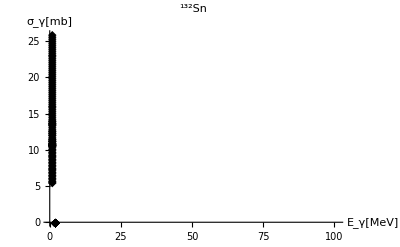

NonlinearModelFit::wts: The value of option Weights -> {4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,«33»,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,«52»} should be a list of real numbers or a pure function.

General::stop: Further output of NonlinearModelFit::wts will be suppressed during this calculation.

-Graphics-

NonlinearModelFit::wts: The value of option Weights -> {4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,«33»,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,«52»} should be a list of real numbers or a pure function.

General::stop: Further output of NonlinearModelFit::wts will be suppressed during this calculation.

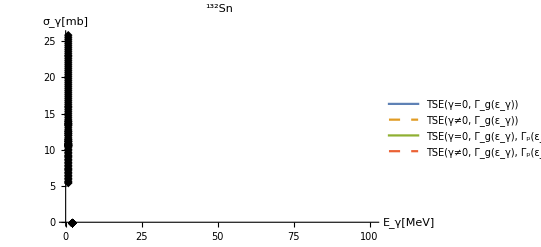

exportSH1.png

NonlinearModelFit::wts: The value of option Weights -> {4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,«33»,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,«52»} should be a list of real numbers or a pure function.

General::stop: Further output of NonlinearModelFit::wts will be suppressed during this calculation.

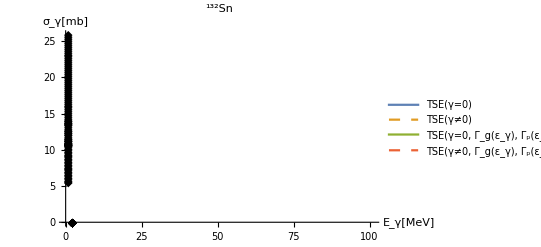

NonlinearModelFit::wts: The value of option Weights -> {4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,«33»,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,4.×10^14,«52»} should be a list of real numbers or a pure function.

General::stop: Further output of NonlinearModelFit::wts will be suppressed during this calculation.

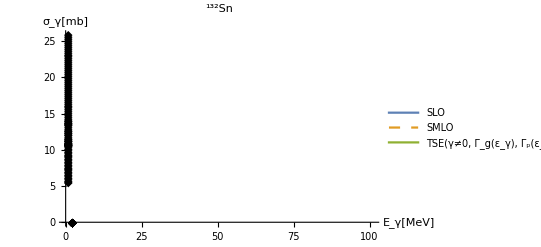

```mathematica
(* Fused *)
errplot2=ErrorListPlot[Data2plotSn132,PlotRange->All,PlotLabel->Style[Row[{Superscript["","132"],"Sn"}],FontFamily->"Times",18,Bold],AxesLabel->{Style[Row[{Subscript["E","γ"],"[MeV]"}],FontFamily->"Times",12,Italic],Style[Row[{Subscript["σ","γ"],"[mb]",""}],FontFamily->"Times",12,Italic]}
, 
PlotStyle->{Black},
PlotMarkers->{◆}
]
Show[errplot2,Plot[FITtemp[x],{x,7,25},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
sh1=Show[errplot2,Plot[{
plot1Data,plot2Data,plot3Data,plot4Data
},{x,7,25},

PlotStyle->{{PointSize[Medium],Glow},{PointSize[Medium],Dashed},PointSize[Medium],{PointSize[Medium],Dashed,Glow}},

PlotLegends->{"TSE(γ=0, Γ_g(ε_γ))","TSE(γ≠0, Γ_g(ε_γ))","TSE(γ=0, Γ_g(ε_γ), Γ_p(ε_γ))","TSE(γ≠0, Γ_g(ε_γ), Γ_p(ε_γ))"},
(*PlotStyle->{Green,Red, Blue,Orange},*)AxesLabel->{Style[Row[{Subscript["E","γ"],""}],FontFamily->"Times",12,Italic],Style[Row[{"S","(",Subscript["E","γ"],")","   ",Superscript["fm","4"],Superscript["MeV","-1"],""}],FontFamily->"Times",12,Italic]},PlotRange->All]]
Export["exportSH1.png",sh1]
Show[errplot2,Plot[{
plot7Data,plot8Data,plot3Data,plot4Data
},{x,7,25},

PlotStyle->{{PointSize[Medium]},{PointSize[Medium],Dashed},PointSize[Medium],{PointSize[Medium],Dashed}},

PlotLegends->{"TSE(γ=0)","TSE(γ≠0)","TSE(γ=0, Γ_g(ε_γ), Γ_p(ε_γ))","TSE(γ≠0, Γ_g(ε_γ), Γ_p(ε_γ))"},
(*PlotStyle->{Green,Red, Blue,Orange},*)AxesLabel->{Style[Row[{Subscript["E","γ"],""}],FontFamily->"Times",12,Italic],Style[Row[{"S","(",Subscript["E","γ"],")","   ",Superscript["fm","4"],Superscript["MeV","-1"],""}],FontFamily->"Times",12,Italic]},PlotRange->All]]

Show[errplot2,Plot[{
plot6Data,plot5Data,plot4Data
},{x,7,25},

PlotStyle->{{PointSize[Medium]},{PointSize[Medium],Dashed},PointSize[Medium],PointSize[Medium],PointSize[Medium]},

PlotLegends->{"SLO","SMLO","TSE(γ≠0, Γ_g(ε_γ), Γ_p(ε_γ))"},
(*PlotStyle->{Green,Red, Blue,Orange},*)AxesLabel->{Style[Row[{Subscript["E","γ"],""}],FontFamily->"Times",12,Italic],Style[Row[{"S","(",Subscript["E","γ"],")","   ",Superscript["fm","4"],Superscript["MeV","-1"],""}],FontFamily->"Times",12,Italic]},PlotRange->All]]
```